```mathematica
ClearAll["Global`*"]
```

```mathematica
fs=FullSimplify;po=PowerExpand;mx=MatrixForm;ft=Flatten;ex=Expand;
```

```mathematica
ODEansatzfull={Derivative[1][Subscript[β,m]][t]==(2 𝒮[t] σ[t] (Subscript[β,max]-Subscript[β,m][t]))/Vs,Derivative[1][σ][t]==(1-f) U λ-(𝒮[t] σ[t]^2)/Vs,Derivative[1][𝒮][t]==b+𝒮[t] (-d+ℐ[t] ((θ σ[t])/Vs-Subscript[β,m][t])),Derivative[1][ℐ][t]==-((ℐ[t] (Vs (d+f U+α)+𝒮[t] (θ σ[t]-Vs Subscript[β,m][t])))/Vs)}
```

{β_m'[t]==(2 𝒮[t] σ[t] (β_max-β_m[t]))/Vs,σ'[t]==(1-f) U λ-(𝒮[t] σ[t]^2)/Vs,𝒮'[t]==b+𝒮[t] (-d+ℐ[t] ((θ σ[t])/Vs-β_m[t])),ℐ'[t]==-(ℐ[t] (Vs (d+f U+α)+𝒮[t] (θ σ[t]-Vs β_m[t])))/Vs}

```mathematica
Thread[ODEansatzfull[[All,1]]==(ODEansatzfull[[All,2]]/.θ->n/2/.Vs->1/Subscript[s, β] //fs)]
```

{β_m'[t]==2 s_β 𝒮[t] σ[t] (β_max-β_m[t]),σ'[t]==-((-1+f) U λ)-s_β 𝒮[t] σ[t]^2,𝒮'[t]==b+1/2 𝒮[t] (n s_β ℐ[t] σ[t]-2 (d+ℐ[t] β_m[t])),ℐ'[t]==-1/2 ℐ[t] (n s_β 𝒮[t] σ[t]+2 (d+f U+α-𝒮[t] β_m[t]))}

```mathematica
varsol = {Subscript[β, m][t], σ[t], 𝒮[t], ℐ[t]}; 
temps = 100; 
paramsall = {Subscript[β, max] -> 4, α -> 2, θ -> 5, b -> 4, d -> 1, α -> 1, Vs -> 1}
U=4;
f=0.4;
λ=0.005;
σclone = 1.*^-8
σstand = (√((1-f) U λ) (-θ √((1-f) U λ)+√((1-f) U θ^2 λ+4 Vs (d+f U+α) Subscript[β, max])))/(2 (d+f U+α))/.μ->(U*f)/.paramsall
σlow = (√((1-f) U λ) (-θ √((1-f) U λ)+√((1-f) U θ^2 λ+4 Vs (d+f U+α) Subscript[β, max])))/(2 (d+f U+α))/.μ->(Ulow*f)/.paramsall

βbar[t_]:=Subscript[β, m][t]-(θ σ[t])/Vs/.paramsall;
fitness[t_]:=βbar[t]𝒮[t]-(d+α+U f)/.paramsall
```

{β_max→4,α→2,θ→5,b→4,d→1,α→1,Vs→1}

1.×10^-8

0.095837

0.095837

```mathematica
scenario="base"
init={Subscript[β, m][0]==OverBar[β0]+(θ σ0)/Vs,σ[0]==σ0,𝒮[0]==b/d,ℐ[0]==0.001}/.{OverBar[β0]->2,σ0->σstand}/.paramsall;
sol:=NDSolve[ft[{ODEansatzfull,init}]//.paramsall,varsol,{t,0,temps}];

pbbar2=Plot[Evaluate[βbar[t]/.sol/.paramsall],{t,0,temps},PlotRange->All,PlotStyle->{Black},PlotLegends->LineLegend[{Black},{"β̄[t] "<>scenario}]];
pfit2=Plot[Evaluate[fitness[t]/.sol/.paramsall],{t,0,temps},PlotRange->All,PlotStyle->{Black},PlotLegends->LineLegend[{Black},{"r[t] "<>scenario}]];
psig2=Plot[Evaluate[σ[t]/. sol],{t,0,temps},PlotRange->All,PlotStyle->{Black},PlotLegends->LineLegend[{Black},{"σ[t] "<>scenario}]];
pb2=Plot[Evaluate[Subscript[β, m][t]/. sol],{t,0,temps},PlotRange->All,PlotStyle->{Black},PlotLegends->LineLegend[{Black},{"β_m[t] "<>scenario}]];
ps2=Plot[Evaluate[𝒮[t]/. sol],{t,0,temps},PlotRange->{0,4},PlotStyle->{Black},PlotLegends->LineLegend[{Black},{"s[t] "<>scenario}]];
pi2=Plot[Evaluate[ℐ[t]/. sol],{t,0,temps},PlotRange->All,PlotStyle->{Dashed, Black},PlotLegends->LineLegend[{Dashed, Black},{"i[t] "<>scenario}]];

p2=Show[psig2,pb2,pbbar2,PlotRange->All];
```

base

```mathematica
scenario="clone"
init={Subscript[β, m][0]==OverBar[β0]+(θ σ0)/Vs,σ[0]==σ0,𝒮[0]==b/d,ℐ[0]==0.001}/.{OverBar[β0]->2,σ0->σclone}/.paramsall;
sol:=NDSolve[ft[{ODEansatzfull,init}]//.paramsall,varsol,{t,0,temps}];

Print[Rinstant];

ps=Plot[Evaluate[𝒮[t]/. sol],{t,0,temps},PlotRange->{0,4},PlotStyle->{Dashed,Red},PlotLegends->LineLegend[{Directive[Red,Dashed]},{"s[t] "<>scenario}]];
pi=Plot[Evaluate[ℐ[t]/. sol],{t,0,temps},PlotRange->All,PlotStyle->{Dashed,Red},PlotLegends->LineLegend[{Directive[Red,Dashed]},{"i[t] "<>scenario}]];
Show[ps,pi];


pbbar=Plot[Evaluate[βbar[t]/.sol/.paramsall],{t,0,temps},PlotRange->All,PlotStyle->{Dashed,Red},PlotLegends->LineLegend[{Directive[Red,Dashed]},{"β̄[t] "<>scenario}]];
pfit=Plot[Evaluate[fitness[t]/.sol/.paramsall],{t,0,temps},PlotRange->All,PlotStyle->{Dashed,Red},PlotLegends->LineLegend[{Directive[Red,Dashed]},{"r[t] "<>scenario}]];
psig=Plot[Evaluate[σ[t]/. sol],{t,0,temps},PlotRange->All,PlotStyle->{Dashed,Red},PlotLegends->LineLegend[{Directive[Red,Dashed]},{"σ[t] "<>scenario}]];
pb=Plot[Evaluate[Subscript[β, m][t]/. sol],{t,0,temps},PlotRange->All,PlotStyle->{Dashed,Red},PlotLegends->LineLegend[{Directive[Red,Dashed]},{"β_m[t] "<>scenario}]];
p1=Show[psig,pb,pbbar];
σ[t]/. sol/.t->temps
```

clone

Rinstant

{0.095837}

```mathematica
scenario="nomut"
Utemp=U
U=0
init={Subscript[β, m][0]==OverBar[β0]+(θ σ0)/Vs,σ[0]==σ0,𝒮[0]==b/d,ℐ[0]==0.001}/.{OverBar[β0]->2,σ0->σstand}/.paramsall;

sol:=NDSolve[ft[{ODEansatzfull,init}]//.paramsall,varsol,{t,0,temps}];
ODEansatzfull
ps4=Plot[Evaluate[𝒮[t]/. sol],{t,0,temps},PlotRange->All,PlotStyle->{Dotted,Black},PlotLegends->LineLegend[{Directive[Black,Dotted]},{"S[t] "<>scenario}]];
pi4=Plot[Evaluate[ℐ[t]/. sol],{t,0,temps},PlotRange->All,PlotStyle->{Dotted,Red},PlotLegends->LineLegend[{Directive[Red,Dotted]},{"I[t] "<>scenario}]];
pepi4=Show[ps4,pi4];



pbbar4=Plot[Evaluate[βbar[t]/.sol/.paramsall],{t,0,temps},PlotRange->All,PlotStyle->{Red},PlotLegends->LineLegend[{Directive[Red]},{"β̄[t] "<>scenario}]];
pfit4=Plot[Evaluate[fitness[t]/.sol/.paramsall],{t,0,temps},PlotRange->All,PlotStyle->{Red},PlotLegends->LineLegend[{Directive[Red]},{"r[t] "<>scenario}]];
psig4=Plot[Evaluate[σ[t]/. sol],{t,0,temps},PlotRange->All,PlotStyle->{Red},PlotLegends->LineLegend[{Directive[Red]},{"σ[t] "<>scenario}]];
pb4=Plot[Evaluate[Subscript[β, m][t]/. sol],{t,0,temps},PlotRange->All,PlotStyle->{Red},PlotLegends->LineLegend[{Directive[Red]},{"β_m[t] "<>scenario}]];


p4=Show[psig4,pb4,pbbar4,PlotRange->All];
Show[p1,p4];
U=Utemp
```

nomut

4

0

{β_m'[t]==(2 𝒮[t] σ[t] (β_max-β_m[t]))/Vs,σ'[t]==0.-(𝒮[t] σ[t]^2)/Vs,𝒮'[t]==b+𝒮[t] (-d+ℐ[t] ((θ σ[t])/Vs-β_m[t])),ℐ'[t]==-(ℐ[t] (Vs (0.+d+α)+𝒮[t] (θ σ[t]-Vs β_m[t])))/Vs}

4

```mathematica
Show[pbbar,pbbar2,pbbar4,Frame->{True,True,False,False},FrameStyle->{Black,Black,Automatic,Automatic},FrameLabel->{{"Mean transmission rate β̄",None},{"Time",None}}];
Export["/home/guillemet/Documents/lethal_mut/work/steps/figures/scenarios_bbar.pdf",%];
Show[pfit,pfit2,pfit4,Frame->{True,True,False,False},FrameStyle->{Black,Black,Automatic,Automatic},FrameLabel->{{"Mean transmission rate β̄",None},{"Time",None}}];
Export["/home/guillemet/Documents/lethal_mut/work/steps/figures/scenarios_fitness.pdf",%];
Show[psig,psig2,psig4,Frame->{True,True,False,False},FrameStyle->{Black,Black,Automatic,Automatic},FrameLabel->{{"Genetic variance σ",None},{"Time",None}}];
Export["/home/guillemet/Documents/lethal_mut/work/steps/figures/scenarios_sig.pdf",%];
Show[pb,pb2,pb4,Frame->{True,True,False,False},FrameStyle->{Black,Black,Automatic,Automatic},FrameLabel->{{"Median transmission rate β(ḡ)",None},{"Time",None}}];
Export["/home/guillemet/Documents/lethal_mut/work/steps/figures/scenarios_b.pdf",%]
Show[ps2,pi2];
Export["/home/guillemet/Documents/lethal_mut/work/steps/figures/scenarios_SI.pdf",%]
```

Export::nodir: Directory /home/guillemet/Documents/lethal_mut/work/steps/figures/ does not exist.

Export::noopen: Cannot open /home/guillemet/Documents/lethal_mut/work/steps/figures/scenarios_bbar.pdf.

Export::nodir: Directory /home/guillemet/Documents/lethal_mut/work/steps/figures/ does not exist.

Export::noopen: Cannot open /home/guillemet/Documents/lethal_mut/work/steps/figures/scenarios_fitness.pdf.

Export::nodir: Directory /home/guillemet/Documents/lethal_mut/work/steps/figures/ does not exist.

Export::noopen: Cannot open /home/guillemet/Documents/lethal_mut/work/steps/figures/scenarios_sig.pdf.

Export::nodir: Directory /home/guillemet/Documents/lethal_mut/work/steps/figures/ does not exist.

Export::noopen: Cannot open /home/guillemet/Documents/lethal_mut/work/steps/figures/scenarios_b.pdf.

$Failed

Export::nodir: Directory /home/guillemet/Documents/lethal_mut/work/steps/figures/ does not exist.

Export::noopen: Cannot open /home/guillemet/Documents/lethal_mut/work/steps/figures/scenarios_SI.pdf.

$Failed

```mathematica
U=.
f=.
λ=.
```

#### mean fitness dynamics

```mathematica
ODEansatzfull={Derivative[1][Subscript[β,m]][t]==(2 𝒮[t] σ[t] (Subscript[β,max]-Subscript[β,m][t]))/Vs,Derivative[1][σ][t]==(1-f) U λ-(𝒮[t] σ[t]^2)/Vs,Derivative[1][𝒮][t]==b+𝒮[t] (-d+ℐ[t] ((θ σ[t])/Vs-Subscript[β,m][t])),Derivative[1][ℐ][t]==-((ℐ[t] (Vs (d+f U+α)+𝒮[t] (θ σ[t]-Vs Subscript[β,m][t])))/Vs)}
```

{β_m'[t]==(2 𝒮[t] σ[t] (β_max-β_m[t]))/Vs,σ'[t]==(1-f) U λ-(𝒮[t] σ[t]^2)/Vs,𝒮'[t]==b+𝒮[t] (-d+ℐ[t] ((θ σ[t])/Vs-β_m[t])),ℐ'[t]==-(ℐ[t] (Vs (d+f U+α)+𝒮[t] (θ σ[t]-Vs β_m[t])))/Vs}

```mathematica
varsol = {Subscript[β, m][t], σ[t], 𝒮[t], ℐ[t]}; 
temps = 40; 
paramsall = {Subscript[β, max] -> 4, α -> 2, θ -> 5, b -> 4, d -> 1, α -> 1, Vs -> 1}
paramsall = {Subscript[β, max] -> 4, α -> 2, θ -> 5, b -> 4, d -> 1, α -> 1, Vs -> 1}
U=4;
Ulow=1
f=0.4;
λ=0.005;
σclone = 1.*^-8
σstand = (√((1-f) U λ) (-θ √((1-f) U λ)+√((1-f) U θ^2 λ+4 Vs (d+f U+α) Subscript[β, max])))/(2 (d+f U+α))/.μ->(U*f)/.paramsall
σlow = (√((1-f) U λ) (-θ √((1-f) U λ)+√((1-f) U θ^2 λ+4 Vs (d+f U+α) Subscript[β, max])))/(2 (d+f U+α))/.U->Ulow/.paramsall

βbar[t_]:=Subscript[β, m][t]-(θ σ[t])/Vs/.paramsall;
fitness[t_]:=βbar[t]𝒮[t]-(d+α+U f)/.paramsall
```

{β_max→4,α→2,θ→5,b→4,d→1,α→1,Vs→1}

{β_max→4,α→2,θ→5,b→4,d→1,α→1,Vs→1}

1

1.×10^-8

0.095837

0.0449683

base

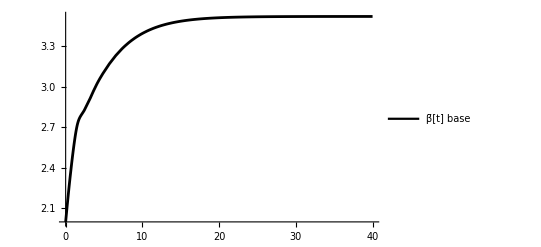

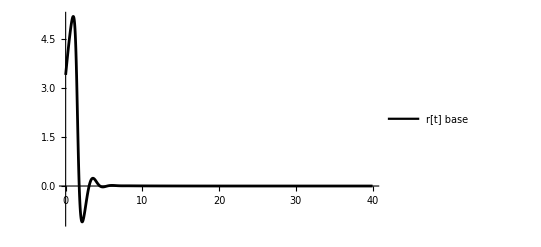

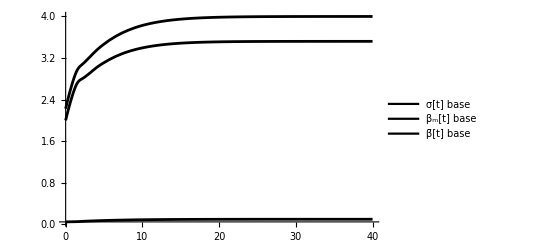

```mathematica
scenario="base"
init={Subscript[β, m][0]==OverBar[β0]+(θ σ0)/Vs,σ[0]==σ0,𝒮[0]==b/d,ℐ[0]==0.001}/.{OverBar[β0]->2,σ0->σlow}/.paramsall;
sol:=NDSolve[ft[{ODEansatzfull,init}]//.paramsall,varsol,{t,0,temps}];

pbbar2=Plot[Evaluate[βbar[t]/.sol/.paramsall],{t,0,temps},PlotRange->All,PlotStyle->{Black},PlotLegends->LineLegend[{Black},{"β̄[t] "<>scenario}]]
pfit2=Plot[Evaluate[fitness[t]/.sol/.paramsall],{t,0,temps},PlotRange->All,PlotStyle->{Black},PlotLegends->LineLegend[{Black},{"r[t] "<>scenario}]]
psig2=Plot[Evaluate[σ[t]/. sol],{t,0,temps},PlotRange->All,PlotStyle->{Black},PlotLegends->LineLegend[{Black},{"σ[t] "<>scenario}]];
pb2=Plot[Evaluate[Subscript[β, m][t]/. sol],{t,0,temps},PlotRange->All,PlotStyle->{Black},PlotLegends->LineLegend[{Black},{"β_m[t] "<>scenario}]];
ps2=Plot[Evaluate[𝒮[t]/. sol],{t,0,temps},PlotRange->{0,4},PlotStyle->{Black},PlotLegends->LineLegend[{Black},{"s[t] "<>scenario}]];
pi2=Plot[Evaluate[ℐ[t]/. sol],{t,0,temps},PlotRange->All,PlotStyle->{Red},PlotLegends->LineLegend[{Red},{"i[t] "<>scenario}]];

p2=Show[psig2,pb2,pbbar2,PlotRange->All]
```

clone

Rinstant

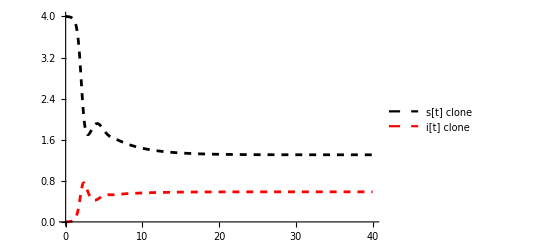

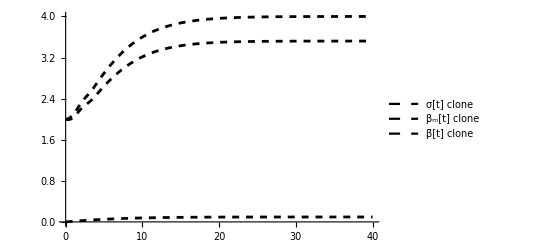

{0.09581}

```mathematica
scenario="clone"
init={Subscript[β, m][0]==OverBar[β0]+(θ σ0)/Vs,σ[0]==σ0,𝒮[0]==b/d,ℐ[0]==0.001}/.{OverBar[β0]->2,σ0->σclone}/.paramsall;
sol:=NDSolve[ft[{ODEansatzfull,init}]//.paramsall,varsol,{t,0,temps}];

Print[Rinstant];

ps=Plot[Evaluate[𝒮[t]/. sol],{t,0,temps},PlotRange->{0,4},PlotStyle->{Dashed,Black},PlotLegends->LineLegend[{Directive[Black,Dashed]},{"s[t] "<>scenario}]];
pi=Plot[Evaluate[ℐ[t]/. sol],{t,0,temps},PlotRange->All,PlotStyle->{Dashed,Red},PlotLegends->LineLegend[{Directive[Red,Dashed]},{"i[t] "<>scenario}]];
Show[ps,pi]


pbbar=Plot[Evaluate[βbar[t]/.sol/.paramsall],{t,0,temps},PlotRange->All,PlotStyle->{Dashed,Black},PlotLegends->LineLegend[{Directive[Black,Dashed]},{"β̄[t] "<>scenario}]];
pfit=Plot[Evaluate[fitness[t]/.sol/.paramsall],{t,0,temps},PlotRange->All,PlotStyle->{Dashed,Black},PlotLegends->LineLegend[{Directive[Black,Dashed]},{"r[t] "<>scenario}]];
psig=Plot[Evaluate[σ[t]/. sol],{t,0,temps},PlotRange->All,PlotStyle->{Dashed,Black},PlotLegends->LineLegend[{Directive[Black,Dashed]},{"σ[t] "<>scenario}]];
pb=Plot[Evaluate[Subscript[β, m][t]/. sol],{t,0,temps},PlotRange->All,PlotStyle->{Dashed,Black},PlotLegends->LineLegend[{Directive[Black,Dashed]},{"β_m[t] "<>scenario}]];
p1=Show[psig,pb,pbbar]
σ[t]/. sol/.t->temps
```

nomut

4

0

{β_m'[t]==(2 𝒮[t] σ[t] (β_max-β_m[t]))/Vs,σ'[t]==0.-(𝒮[t] σ[t]^2)/Vs,𝒮'[t]==b+𝒮[t] (-d+ℐ[t] ((θ σ[t])/Vs-β_m[t])),ℐ'[t]==-(ℐ[t] (Vs (0.+d+α)+𝒮[t] (θ σ[t]-Vs β_m[t])))/Vs}

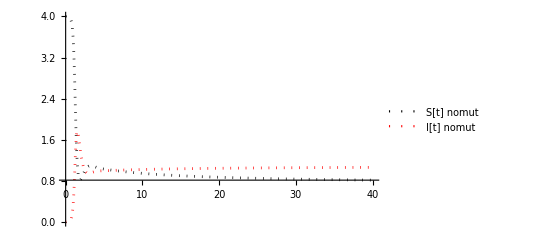

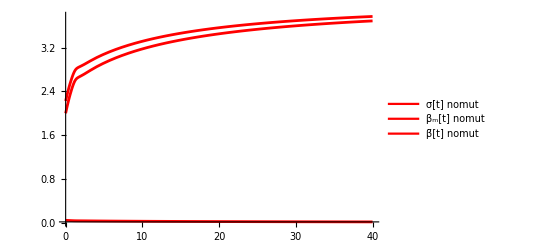

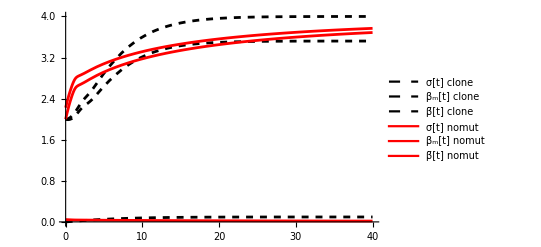

4

```mathematica
scenario="nomut"
Utemp=U
U=0
init={Subscript[β, m][0]==OverBar[β0]+(θ σ0)/Vs,σ[0]==σ0,𝒮[0]==b/d,ℐ[0]==0.001}/.{OverBar[β0]->2,σ0->σlow}/.paramsall;

sol:=NDSolve[ft[{ODEansatzfull,init}]//.paramsall,varsol,{t,0,temps}]
ODEansatzfull
ps4=Plot[Evaluate[𝒮[t]/. sol],{t,0,temps},PlotRange->All,PlotStyle->{Dotted,Black},PlotLegends->LineLegend[{Directive[Black,Dotted]},{"S[t] "<>scenario}]];
pi4=Plot[Evaluate[ℐ[t]/. sol],{t,0,temps},PlotRange->All,PlotStyle->{Dotted,Red},PlotLegends->LineLegend[{Directive[Red,Dotted]},{"I[t] "<>scenario}]];
pepi4=Show[ps4,pi4]



pbbar4=Plot[Evaluate[βbar[t]/.sol/.paramsall],{t,0,temps},PlotRange->All,PlotStyle->{Red},PlotLegends->LineLegend[{Directive[Red]},{"β̄[t] "<>scenario}]];
pfit4=Plot[Evaluate[fitness[t]/.sol/.paramsall],{t,0,temps},PlotRange->All,PlotStyle->{Red},PlotLegends->LineLegend[{Directive[Red]},{"r[t] "<>scenario}]];
psig4=Plot[Evaluate[σ[t]/. sol],{t,0,temps},PlotRange->All,PlotStyle->{Red},PlotLegends->LineLegend[{Directive[Red]},{"σ[t] "<>scenario}]];
pb4=Plot[Evaluate[Subscript[β, m][t]/. sol],{t,0,temps},PlotRange->All,PlotStyle->{Red},PlotLegends->LineLegend[{Directive[Red]},{"β_m[t] "<>scenario}]];


p4=Show[psig4,pb4,pbbar4,PlotRange->All]
Show[p1,p4]
U=Utemp
```

```mathematica
pbbar2
```

-Graphics-

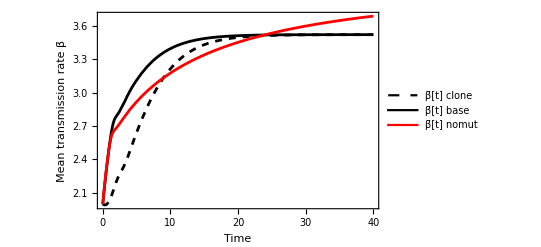

Export::nodir: Directory /home/guillemet/Documents/lethal_mut/work/steps/figures/ does not exist.

Export::noopen: Cannot open /home/guillemet/Documents/lethal_mut/work/steps/figures/scenariosLow_bbar.pdf.

$Failed

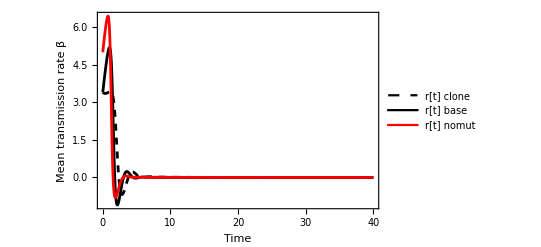

Export::nodir: Directory /home/guillemet/Documents/lethal_mut/work/steps/figures/ does not exist.

Export::noopen: Cannot open /home/guillemet/Documents/lethal_mut/work/steps/figures/scenariosLow_fitness.pdf.

$Failed

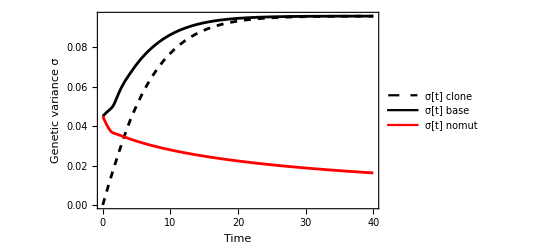

Export::nodir: Directory /home/guillemet/Documents/lethal_mut/work/steps/figures/ does not exist.

Export::noopen: Cannot open /home/guillemet/Documents/lethal_mut/work/steps/figures/scenariosLow_sig.pdf.

$Failed

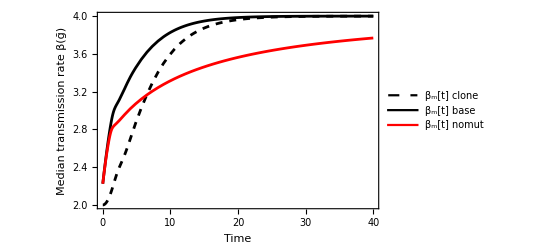

Export::nodir: Directory /home/guillemet/Documents/lethal_mut/work/steps/figures/ does not exist.

Export::noopen: Cannot open /home/guillemet/Documents/lethal_mut/work/steps/figures/scenariosLow_b.pdf.

$Failed

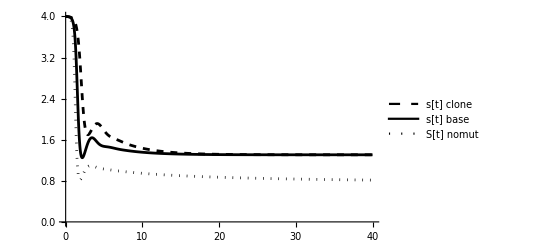

```mathematica
Show[pbbar,pbbar2,pbbar4,Frame->{True,True,False,False},FrameStyle->{Black,Black,Automatic,Automatic},FrameLabel->{{"Mean transmission rate β̄",None},{"Time",None}}]
Export["/home/guillemet/Documents/lethal_mut/work/steps/figures/scenariosLow_bbar.pdf",%]
Show[pfit,pfit2,pfit4,Frame->{True,True,False,False},FrameStyle->{Black,Black,Automatic,Automatic},FrameLabel->{{"Mean transmission rate β̄",None},{"Time",None}}]
Export["/home/guillemet/Documents/lethal_mut/work/steps/figures/scenariosLow_fitness.pdf",%]
Show[psig,psig2,psig4,Frame->{True,True,False,False},FrameStyle->{Black,Black,Automatic,Automatic},FrameLabel->{{"Genetic variance σ",None},{"Time",None}}]
Export["/home/guillemet/Documents/lethal_mut/work/steps/figures/scenariosLow_sig.pdf",%]
Show[pb,pb2,pb4,Frame->{True,True,False,False},FrameStyle->{Black,Black,Automatic,Automatic},FrameLabel->{{"Median transmission rate β(ḡ)",None},{"Time",None}}]
Export["/home/guillemet/Documents/lethal_mut/work/steps/figures/scenariosLow_b.pdf",%]
Show[ps,ps2,ps4]
```

```mathematica
U=.
f=.
λ=.
```

#### Varying β̄ through β(ḡ)

```mathematica
βbar[t_]:=Subscript[β, m][t]-(n σ[t])/(2 Vs)/.paramsall;


start1=0.6
start2=0.9

scenario="betabeta1"
U=.;
f=.;
λ=.;
temps=80;
t0l=0.032
varsol = {Subscript[β, m][t], σ[t], 𝒮[t], ℐ[t]}; 
(*paramsall = {Vs->1,λ->0.005,g->-0,n->5,Subscript[β, max] -> 4, α -> 2, b -> 4, d -> 1, U->2, f->0.4,θ->n/2};*)
paramsall = {Vs->1,λ->0.05,g->-0,n->5,Subscript[β, max] -> 4, α -> 2, b -> 3, d -> 1, U->2, f->0.4,θ->n/2}; (* new after review *)
init={Subscript[β, m][0]==OverBar[β0],σ[0]==σ0,𝒮[0]==b/d,ℐ[0]==0.1}/.{OverBar[β0]->4-5/2*start1^2,σ0->σclone}//.paramsall;
ODEansatzfullNodem=ft[{ODEansatzfull[[{1,2,4}]],𝒮'[t]==0}];
sol:=NDSolve[ft[{ODEansatzfull,init}]//.paramsall,varsol,{t,0,temps}];
ps6=Plot[Evaluate[𝒮[t]/. sol],{t,0,temps},PlotRange->All,PlotStyle->{Black},PlotLegends->LineLegend[{Directive[Black]},{"S[t] "<>scenario}]];
pi6=Plot[Evaluate[ℐ[t]/. sol],{t,0,temps},PlotRange->All,PlotStyle->{Red},PlotLegends->LineLegend[{Directive[Red]},{"I[t] "<>scenario}]];
pepi6=Show[ps6,pi6];



pbbar6=Plot[Evaluate[βbar[t]/.sol/.paramsall],{t,0,temps},PlotRange->All,PlotStyle->{Black}];
pbbar6l=LogLinearPlot[Evaluate[βbar[t]/.sol/.paramsall],{t,t0l,temps},PlotRange->All,PlotStyle->{Black}];
psig6=Plot[Evaluate[σ[t]/. sol],{t,0,temps},PlotRange->All,PlotStyle->{Black},PlotLegends->LineLegend[{Directive[Black]},{"σ[t] "<>scenario}]];
pb6=Plot[Evaluate[Subscript[β, m][t]/. sol],{t,0,temps},PlotRange->All,PlotStyle->{Orange},PlotLegends->LineLegend[{Directive[Orange]},{"β_m[t] "<>scenario}]];


p6=Show[psig6,pb6,pbbar6,PlotRange->All];
(Subscript[β, m][t]-(θ σ[t])/Vs)//.paramsall/.sol/.t->0//First/.t->0
```

0.6

0.9

betabeta1

0.032

3.1

```mathematica
scenario="betabeta1"
init={Subscript[β, m][0]==OverBar[β0],σ[0]==σ0,𝒮[0]==b/d,ℐ[0]==0.1}/.{OverBar[β0]->3,σ0->σclone}//.paramsall;

sol:=NDSolve[ft[{ODEansatzfull,init}]//.paramsall,varsol,{t,0,temps}];


ps7=Plot[Evaluate[𝒮[t]/. sol],{t,0,temps},PlotRange->All,PlotStyle->{Black},PlotLegends->LineLegend[{Directive[Black]},{"S[t] "<>scenario}]];
pi7=Plot[Evaluate[ℐ[t]/. sol],{t,0,temps},PlotRange->All,PlotStyle->{Red},PlotLegends->LineLegend[{Directive[Red]},{"I[t] "<>scenario}]];
pepi7=Show[ps7,pi7];



pbbar7l=LogLinearPlot[Evaluate[βbar[t]/.sol/.paramsall],{t,t0l,temps},PlotRange->All,PlotStyle->{Black}];
pbbar7=Plot[Evaluate[βbar[t]/.sol/.paramsall],{t,0,temps},PlotRange->All,PlotStyle->{Black}];
psig7=Plot[Evaluate[σ[t]/. sol],{t,0,temps},PlotRange->All,PlotStyle->{Black},PlotLegends->LineLegend[{Directive[Black]},{"σ[t] "<>scenario}]];
pb7=Plot[Evaluate[Subscript[β, m][t]/. sol],{t,0,temps},PlotRange->All,PlotStyle->{Orange},PlotLegends->LineLegend[{Directive[Orange]},{"β_m[t] "<>scenario}]];


p7=Show[psig7,pb7,pbbar7,PlotRange->All];
```

betabeta1

betabeta1

{β_m[0]==1.975,σ[0]==1.×10^-8,𝒮[0]==3,ℐ[0]==0.1}

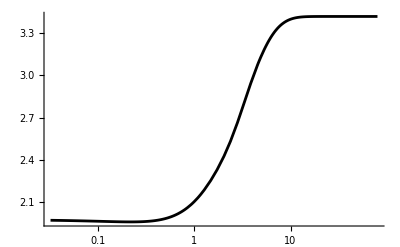

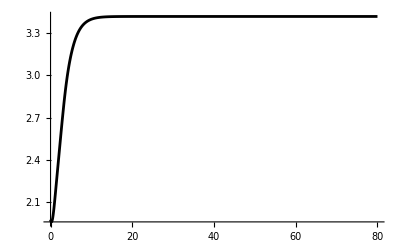

1.975

3.41913

```mathematica
scenario="betabeta1"
init={Subscript[β, m][0]==OverBar[β0],σ[0]==σ0,𝒮[0]==b/d,ℐ[0]==0.1}/.{OverBar[β0]->4-5/2*start2^2,σ0->σclone}//.paramsall

sol:=NDSolve[ft[{ODEansatzfull,init}]//.paramsall,varsol,{t,0,temps}];

ps8=Plot[Evaluate[𝒮[t]/. sol],{t,0,temps},PlotRange->All,PlotStyle->{Black},PlotLegends->LineLegend[{Directive[Black]},{"S[t] "<>scenario}]];
pi8=Plot[Evaluate[ℐ[t]/. sol],{t,0,temps},PlotRange->All,PlotStyle->{Red},PlotLegends->LineLegend[{Directive[Red]},{"I[t] "<>scenario}]];
pepi8=Show[ps8,pi8];


pbbar8l=LogLinearPlot[Evaluate[βbar[t]/.sol/.paramsall],{t,t0l,temps},PlotRange->All,PlotStyle->{Black}]
pbbar8=Plot[Evaluate[βbar[t]/.sol/.paramsall],{t,0,temps},PlotRange->All,PlotStyle->{Black}]
psig8=Plot[Evaluate[σ[t]/. sol],{t,0,temps},PlotRange->All,PlotStyle->{Black},PlotLegends->LineLegend[{Directive[Black]},{"σ[t] "<>scenario}]];
pb8=Plot[Evaluate[Subscript[β, m][t]/. sol],{t,0,temps},PlotRange->All,PlotStyle->{Orange},PlotLegends->LineLegend[{Directive[Orange]},{"β_m[t] "<>scenario}]];


p8=Show[psig8,pb8,pbbar8,PlotRange->All];
(Subscript[β, m][t]-(θ σ[t])/Vs)//.paramsall/.sol/.t->0//First/.t->0
(Subscript[β, m][t]-(θ σ[t])/Vs)//.paramsall/.sol/.t->temps//First/.t->temps
```

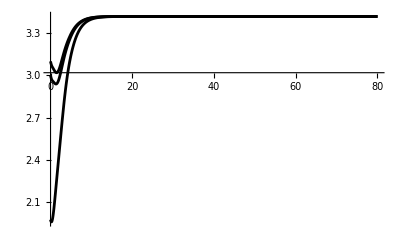

```mathematica
Show[pbbar6,pbbar7,pbbar8]
```

```mathematica
U=.
f=.
λ=.
```

#### Varying β̄ through σ

```mathematica
scenario="betasigma2"

sigmastart=0.15

init={Subscript[β, m][0]==OverBar[β0],σ[0]==σ0,𝒮[0]==b/d,ℐ[0]==0.1}/.{OverBar[β0]->4-5/2*start1^2,σ0->sigmastart}//.paramsall;

sol:=NDSolve[ft[{ODEansatzfull,init}]//.paramsall,varsol,{t,0,temps}];

ps10=Plot[Evaluate[𝒮[t]/. sol],{t,0,temps},PlotRange->All,PlotStyle->{Black},PlotLegends->LineLegend[{Directive[Black]},{"S[t] "<>scenario}]];
pi10=Plot[Evaluate[ℐ[t]/. sol],{t,0,temps},PlotRange->All,PlotStyle->{Red},PlotLegends->LineLegend[{Directive[Red]},{"I[t] "<>scenario}]];
pepi10=Show[ps10,pi10];


pbbar10=Plot[Evaluate[βbar[t]/.sol/.paramsall],{t,0,temps},PlotRange->All,PlotStyle->{Black, Dashing[{0.008,Small}]}];
pbbar10l=LogLinearPlot[Evaluate[βbar[t]/.sol/.paramsall],{t,t0l,temps},PlotRange->All,PlotStyle->{Black, Dashing[{0.008,Small}]}];
psig10=Plot[Evaluate[σ[t]/. sol],{t,0,temps},PlotRange->All,PlotStyle->{Black},PlotLegends->LineLegend[{Directive[Black]},{"σ[t] "<>scenario}]];
pb10=Plot[Evaluate[Subscript[β, m][t]/. sol],{t,0,temps},PlotRange->All,PlotStyle->{Orange},PlotLegends->LineLegend[{Directive[Orange]},{"β_m[t] "<>scenario}]];


p10=Show[psig10,pb10,pbbar10,PlotRange->All];
(Subscript[β, m][t]-(θ σ[t])/Vs)//.paramsall/.sol/.t->0//First/.t->0
```

betasigma2

0.15

2.725

```mathematica
(*scenario="betasigma3"

βbar[t]
init={Subscript[β, m][0]==OverBar[β0],σ[0]==σ0,𝒮[0]==b/d,ℐ[0]==0.1}/.{OverBar[β0]->4-5/2*start1^2,σ0->sigmastart}//.paramsall;

sol:=NDSolve[ft[{ODEansatzfull,init}]//.paramsall,varsol,{t,0,temps}];

ps11=Plot[Evaluate[𝒮[t]/. sol],{t,0,temps},PlotRange->All,PlotStyle->{Black},PlotLegends->LineLegend[{Directive[Black]},{"S[t] "<>scenario}]];
pi11=Plot[Evaluate[ℐ[t]/. sol],{t,0,temps},PlotRange->All,PlotStyle->{Red},PlotLegends->LineLegend[{Directive[Red]},{"I[t] "<>scenario}]];
pepi11=Show[ps11,pi11];


pbbar11=Plot[Evaluate[βbar[t]/.sol/.paramsall],{t,0,temps},PlotRange->All,PlotStyle->{Black, Dashing[{0.008,Small}]}]
pbbar11l=LogLinearPlot[Evaluate[βbar[t]/.sol/.paramsall],{t,t0l,temps},PlotRange->All,PlotStyle->{Black, Dashing[{0.008,Small}]}]
psig11=Plot[Evaluate[σ[t]/. sol],{t,0,temps},PlotRange->All,PlotStyle->{Black},PlotLegends->LineLegend[{Directive[Black]},{"σ[t] "<>scenario}]];
pb11=Plot[Evaluate[Subscript[β, m][t]/. sol],{t,0,temps},PlotRange->All,PlotStyle->{Orange},PlotLegends->LineLegend[{Directive[Orange]},{"β_m[t] "<>scenario}]];


p11=Show[psig11,pb11,pbbar11,PlotRange->All];*)
```

betasigma4

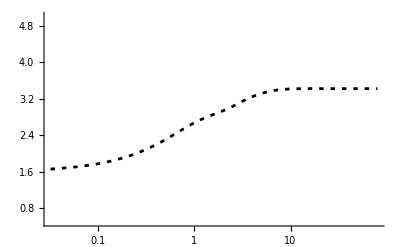

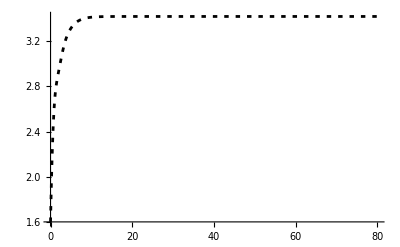

1.6

```mathematica
scenario="betasigma4"

init={Subscript[β, m][0]==OverBar[β0],σ[0]==σ0,𝒮[0]==b/d,ℐ[0]==0.1}/.{OverBar[β0]->4-5/2*start2^2,σ0->sigmastart}//.paramsall;

sol:=NDSolve[ft[{ODEansatzfull,init}]//.paramsall,varsol,{t,0,temps}];

ps12=Plot[Evaluate[𝒮[t]/. sol],{t,0,temps},PlotRange->All,PlotStyle->{Black},PlotLegends->LineLegend[{Directive[Black]},{"S[t] "<>scenario}]];
pi12=Plot[Evaluate[ℐ[t]/. sol],{t,0,temps},PlotRange->All,PlotStyle->{Red},PlotLegends->LineLegend[{Directive[Red]},{"I[t] "<>scenario}]];
pepi12=Show[ps12,pi12];


pbbar12l=LogLinearPlot[Evaluate[βbar[t]/.sol/.paramsall],{t,t0l,temps},PlotRange->{All,{0.5,5}},PlotStyle->{Black, Dashing[{0.008,Small}]}]
pbbar12=Plot[Evaluate[βbar[t]/.sol/.paramsall],{t,0,temps},PlotRange->All,PlotStyle->{Black, Dashing[{0.008,Small}]}]
psig12=Plot[Evaluate[σ[t]/. sol],{t,0,temps},PlotRange->All,PlotStyle->{Black, Dashing[{0.008,Small}]},PlotLegends->LineLegend[{Directive[Black]},{"σ[t] "<>scenario}]];
pb12=Plot[Evaluate[Subscript[β, m][t]/. sol],{t,0,temps},PlotRange->All,PlotStyle->{Orange},PlotLegends->LineLegend[{Directive[Orange]},{"β_m[t] "<>scenario}]];


p12=Show[psig12,pb12,pbbar12,PlotRange->All];
(Subscript[β, m][t]-(θ σ[t])/Vs)//.paramsall/.sol/.t->0//First/.t->0
```

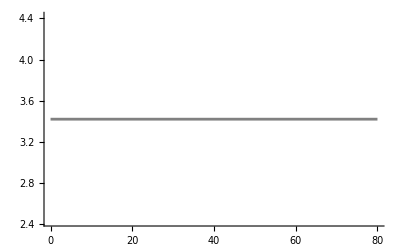

```mathematica
eqsol = sol:=NDSolve[ft[{ODEansatzfull,init}]//.paramsall,varsol,{t,0,1000}];
pbbareq=Plot[Evaluate[βbar[t]/.sol/.paramsall/.t->999],{t,0,temps},PlotRange->All,PlotStyle->{Gray}]
bbareq = βbar[t]/.sol/.paramsall/.t->999 //First;
pbbareq = Graphics[{Opacity[0.5,Gray],Rectangle[{0,bbareq},{40,4}]}];
```

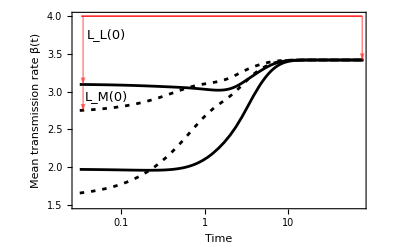

/Users/martin/Documents/lethal/figures/betabar/diffbeta_diffsigma_log.pdf

{Vs→1,λ→0.05,g→0,n→5,β_max→4,α→2,b→3,d→1,U→2,f→0.4,θ→n/2}

```mathematica
text0 = Graphics[Text[Style["β_0",13],{-3.4,4.03}]];
text1 = Graphics[Text[Style["L_M^*",13],{42,3.9}]];
text2 = Graphics[Text[Style["L_M(0)",13],{0.05,3.4}]];
arr = Graphics[{Gray,Thick,{Arrowheads[Medium],Arrow[{{40,4},{40,3.78}}]}}];
ll = Graphics[{Gray,Thick,Line[{{40,4},{0,4}}]}];


(*Show[pbbar10,pbbar11,pbbar12, PlotRange->All, Frame->{True,True,False,False},FrameStyle->{Black,Black,Automatic,Automatic}, FrameLabel->{"Time","β̄(t)"}];

Export["/home/guillemet/Documents/lethal_mut/work/steps/figures/diffbeta_sigma.pdf",%]
Show[pbbar8,pbbar6,pbbar7, PlotRange->All, Frame->{True,True,False,False},FrameStyle->{Black,Black,Automatic,Automatic}, FrameLabel->{"Time","β̄(t)"}];

Export["/home/guillemet/Documents/lethal_mut/work/steps/figures/diffbeta_betam.pdf",%]*)

(*
Show[pbbar12,pbbar10,pbbar11,pbbar8,pbbar6,pbbar7,text0,text1,arr,ll,  Frame->{True,True,False,False},FrameStyle->{Black,Black,Automatic,Automatic}, FrameLabel->{Style["Time",13],Style["Mean transmission rate β̄(t)",13]}, PlotRange->{{0,40},{All,4}},ImagePadding->45
,PlotRangeClipping->False, ImageSize->400,PlotRangePadding->0]

Export["/Users/martin/Documents/lethal/figures/betabar/diffbeta_diffsigma.pdf",%]*)

text0 = Graphics[Text[Style["β_0",13,Red],{-4.15,4.02}]];
text1 = Graphics[Text[Style["L_M^*",13],{4.8,3.7}]];
text2 = Graphics[Text[Style["L_M(0)",13],{-2.7,2.935}]];
arr2 = Graphics[{Opacity[0.5,Red],Thick,{Arrowheads[Medium],Arrow[{{-3.35,3.07},{-3.35,2.75}}]}}];
text3 = Graphics[Text[Style["L_L(0)",13],{-2.7,3.75}]];
arr3 = Graphics[{Opacity[0.5,Red],Thick,{Arrowheads[Medium],Arrow[{{-3.35,4},{-3.35,3.1}}]}}];
arr = Graphics[{Opacity[0.5,Red],Thick,{Arrowheads[Medium],Arrow[{{4.35,4},{4.35,3.42}}]}}];
ll = Graphics[{Red,Thick,Line[{{4.35,4},{-3.4,4}}]}];


(*Show[pbbar12l,pbbar10l,pbbar8l,pbbar6l,text0,arr,ll,text1 , Frame->{True,True,False,False},FrameStyle->{Black,Black,Automatic,Automatic}, FrameLabel->{Style["Time",13],Style["Mean transmission rate β̄(t)",13]}, PlotRange->{{-3.4,3.8},{1.9,4}},ImagePadding->45
,PlotRangeClipping->False, ImageSize->400,PlotRangePadding->0]
*)

Show[pbbar12l,pbbar10l,pbbar8l,pbbar6l,text0,arr,ll,text1 ,text2,text3,arr3,arr2, Frame->{True,True,False,False},FrameStyle->{Black,Black,Black}, FrameLabel->{Style["Time",13],Style["Mean transmission rate β̄(t)",13]}, PlotRange->{{-3.5,4.3},{1.5,4.0}},ImagePadding->45
, ImageSize->400,PlotRangeClipping->False,PlotRangePadding->0]
Export["/Users/martin/Documents/lethal/figures/betabar/diffbeta_diffsigma_log.pdf",%]
paramsall
```

```mathematica
U=.
f=.
λ=.
```

#### dynamics of mean fitness

base

0.8

0.244949

1.×10^-8

{β_max→4,α→2,θ→5,b→4,d→1,α→1,Vs→1}

25

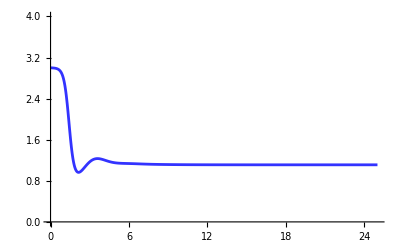

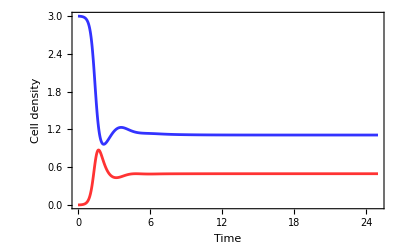

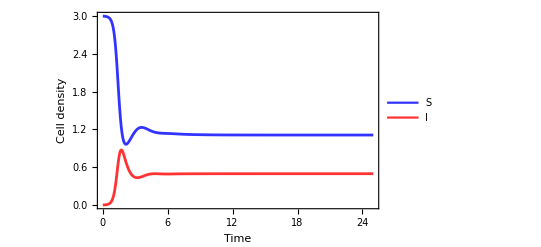

/Users/martin/Documents/lethal/figures/betabar/mean_fitness_SI.pdf

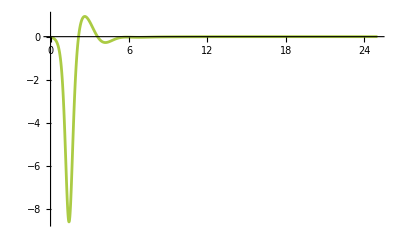

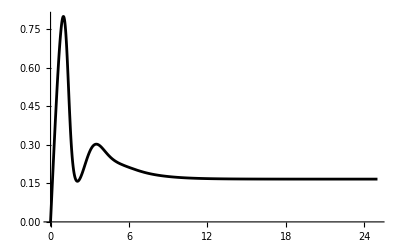

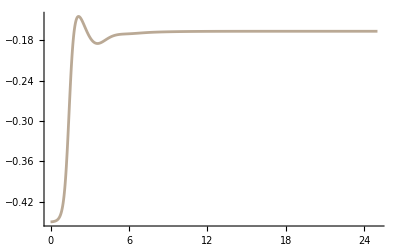

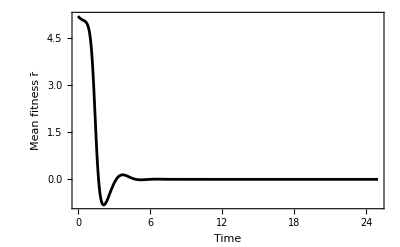

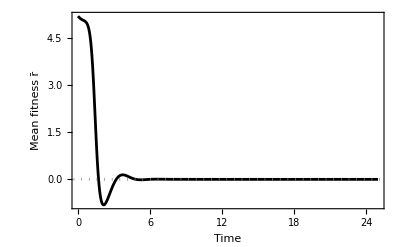

/Users/martin/Documents/lethal/figures/betabar/mean_fitness.pdf

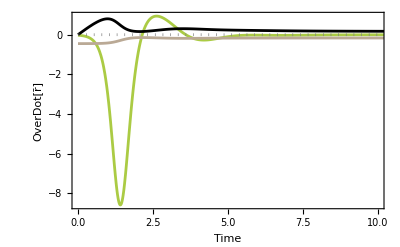

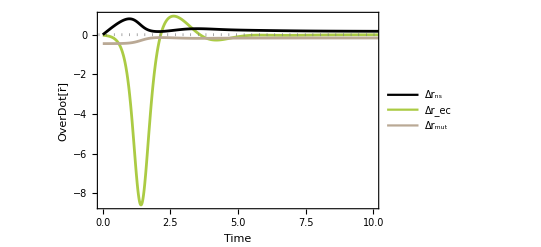

/Users/martin/Documents/lethal/figures/betabar/mean_fitness_dynamics.pdf

```mathematica
scenario="base"

op=0.8
U=2;
f=0.4;
λ=0.005;
λ=0.05;(* new after review *)
μ=Sqrt[U λ (1-f)]
σclone = 1.*^-8
paramsall
temps=25
(*paramsall = {Subscript[β, max] -> 4, α -> 2, θ -> 5, b -> 3, d -> 1, α -> 1, Vs -> 1}*)
paramsall = {Vs->1,λ->0.05,g->-0,n->5,Subscript[β, max] -> 4, α -> 2, b -> 3, d -> 1, U->2, f->0.4,θ->2.5}; (* new after review *)
init={Subscript[β, m][0]==OverBar[β0]+(θ σ0)/Vs,σ[0]==σ0,𝒮[0]==b/d,ℐ[0]==0.001}/.{OverBar[β0]->3,σ0->σclone}/.paramsall;
sol:=NDSolve[ft[{ODEansatzfull,init}]//.paramsall,varsol,{t,0,temps}];

pbbar2=Plot[Evaluate[βbar[t]/.sol/.paramsall],{t,0,temps},PlotRange->All,PlotStyle->{Black},PlotLegends->LineLegend[{Black},{"β̄[t] "<>scenario}]];
pfit2=Plot[Evaluate[fitness[t]/.sol/.paramsall],{t,0,temps},PlotRange->All,PlotStyle->{Black},PlotLegends->LineLegend[{Black},{"r[t] "<>scenario}]];
psig2=Plot[Evaluate[σ[t]/. sol],{t,0,temps},PlotRange->All,PlotStyle->{Black},PlotLegends->LineLegend[{Black},{"σ[t] "<>scenario}]];
pb2=Plot[Evaluate[Subscript[β, m][t]/. sol],{t,0,temps},PlotRange->All,PlotStyle->{Black},PlotLegends->LineLegend[{Black},{"β_m[t] "<>scenario}]];
ps2=Plot[Evaluate[𝒮[t]/. sol],{t,0,temps},PlotRange->{0,4},PlotStyle->{Opacity[op,Blue]}]



pi2=Plot[Evaluate[ℐ[t]/. sol],{t,0,temps},PlotRange->All,PlotStyle->{Opacity[op,Red]}];


pdem=Show[ps2,pi2,  Frame->{True,True,True,True},FrameStyle->{Black,Black,Black,Black}, FrameLabel->{Style["Time",14],Style["Cell density",14]}, Axes->False, PlotRange->{{0,temps},All} ]

Legended[pdem,Placed[LineLegend[{Opacity[op,Blue],Opacity[op,Red]},{Style["S",14],Style["I",14]}, LegendFunction->(Framed[#,FrameStyle->Directive[Gray,Thickness@0.2]]&)],{Right,Top}]]

Export["/Users/martin/Documents/lethal/figures/betabar/mean_fitness_SI.pdf",%]

p2=Show[psig2,pb2,pbbar2,PlotRange->All];




pfitEC=pi2=Plot[Evaluate[((-θ σ[t]+Vs Subscript[β, m][t]) (b Vs-𝒮[t] (d Vs+ℐ[t] (-θ σ[t]+Vs Subscript[β, m][t]))))/Vs^2/.paramsall/. sol],{t,0,temps},PlotRange->All,PlotStyle->{RGBColor["#ABCB44"]}]
pfitNS=Plot[Evaluate[(𝒮[t]^2 σ[t] (2 Vs Subscript[β, max]+θ σ[t]-2 Vs Subscript[β, m][t]))/Vs^2/.paramsall/. sol],{t,0,temps},PlotRange->All,PlotStyle->{Black}]
pfitMUT=Plot[Evaluate[-(θ μ^2 𝒮[t])/Vs/.paramsall/. sol],{t,0,temps},PlotRange->All,PlotStyle->{RGBColor["#BAA995"]}]
pi2=Plot[Evaluate[-((b+𝒮[t] (-d+ℐ[t] ((θ σ[t])/Vs-Subscript[β, m][t]))) (θ σ[t]-Vs Subscript[β, m][t])+(𝒮[t] (Vs θ μ^2-𝒮[t] σ[t] (2 Vs Subscript[β, max]+θ σ[t]-2 Vs Subscript[β, m][t])))/Vs)/Vs/.paramsall/. sol],{t,0,temps},PlotRange->All,PlotStyle->{Red},PlotLegends->LineLegend[{Red},{"fit all"<>scenario}]];
pi2=Plot[Evaluate[βbar[t]𝒮[t]-(α + d + U f)/.paramsall/. sol],{t,0,temps},PlotRange->All,PlotStyle->{Black}, Frame->{True,True,True,True},FrameStyle->{Black,Black,Black,Black}, FrameLabel->{Style["Time",14],Style["Mean fitness r̄",14]}, Axes->False]

aaa=Show[pi2,Plot[0,{x,0-1,temps+1},PlotStyle->{Gray,Dotted}], PlotRange->{{0,temps},All}]

Export["/Users/martin/Documents/lethal/figures/betabar/mean_fitness.pdf",%]

bbb=Show[pfitEC,pfitNS,pfitMUT,Plot[0,{x,0-1,temps+1},PlotStyle->{Gray,Dotted}], Frame->{True,True,True,True},FrameStyle->{Black,Black,Black,Black}, FrameLabel->{Style["Time",14],Style["OverDot[r̄]",14]}, Axes->False, PlotRange->{{0,10},All}]
Legended[bbb,Placed[LineLegend[{Black,RGBColor["#ABCB44"],RGBColor["#BAA995"]},{Style["Δr_ns",14],Style["Δr_ec",14],Style["Δr_mut",14]}, LegendFunction->(Framed[#,FrameStyle->Directive[Gray,Thickness@0.2]]&)],{Right,Bottom}]]


Export["/Users/martin/Documents/lethal/figures/betabar/mean_fitness_dynamics.pdf",%]
```

#### Mutagenic treatment CHRONIC

colors

```mathematica
hexToRGB=RGBColor@@(IntegerDigits[#~StringDrop~1~FromDigits~16,256,3]/255.)&
x0=1.2
x1=1.05
x2=0.83
x3=0.7

c0=Opacity[0.9,RGBColor[0.74*x0,0.83*x0,0.711*x0]]
c1=Opacity[0.9,RGBColor[0.74*x1,0.83*x1,0.711*x1]]
c2=Opacity[0.9,RGBColor[0.74*x2,0.83*x2,0.711*x2]]
c3=Opacity[0.9,RGBColor[0.74*x3,0.83*x3,0.711*x3]]
c4=RGBColor[0.2,0.34,0.36]
```

RGBColor@@IntegerDigits[FromDigits[StringDrop[#1,1],16],256,3]/255.&

1.2

1.05

0.83

0.7

Opacity[0.9,RGBColor[0.888, 0.9959999999999999, 0.8532]]

Opacity[0.9,RGBColor[0.777, 0.8714999999999999, 0.74655]]

Opacity[0.9,RGBColor[0.6142, 0.6889, 0.5901299999999999]]

Opacity[0.9,RGBColor[0.518, 0.581, 0.4976999999999999]]

RGBColor[0.2, 0.34, 0.36]

```mathematica
paramsall = {Subscript[β, max] -> 4, α -> 2, θ -> 5, b -> 3, d -> 1,  Vs -> 1,f->0.4, λ->0.05}

ϵ=0.02
t1=0  (*Start treatment*)
t2=2 (*stop treatment*)
t3=10

betastart=4-5*0.7^2
i0=b/(d+α+U*f)-d/betastart/.paramsall/.U->1
s0=(d+α+U f)/betastart/.paramsall /.U->1
U=.
temps=3
f=.
λ=.
```

{β_max→4,α→2,θ→5,b→3,d→1,Vs→1,0.4→0.4,0.005→0.05}

0.02

0

2

10

1.55

0.00701262

2.96774

3

```mathematica
paramsall = {Subscript[β, max] -> 4, α -> 2, θ -> 5, b -> 3, d -> 1,  Vs -> 1,f->0.4, λ->0.05}
sol1=NDSolve[ft[{ODEansatzfull /. U-> 1,init}]//.paramsall,varsol,{t,0,t2-t1}]
 NDSolve[ft[{ODEansatzfull /. U-> 1,{Subscript[β, m][0]==Subscript[β, m][t]/.sol1/.t->t2-t1,σ[0]==σ[t]/.sol1/.t->t2-t1,𝒮[0]==𝒮[t]/.sol1/.t->t2-t1,ℐ[0]==ℐ[t]/.sol1/.t->t2-t1}/.paramsall}]//.paramsall,varsol,{t,0,t3-t2}]
```

{β_max→4,α→2,θ→5,b→3,d→1,Vs→1,f→0.4,λ→0.05}

{{β_m[t]→InterpolatingFunction[…][t],σ[t]→InterpolatingFunction[…][t],𝒮[t]→InterpolatingFunction[…][t],ℐ[t]→InterpolatingFunction[…][t]}}

{{β_m[t]→InterpolatingFunction[…][t],σ[t]→InterpolatingFunction[…][t],𝒮[t]→InterpolatingFunction[…][t],ℐ[t]→InterpolatingFunction[…][t]}}

{β_max→4,α→2,θ→5,b→3,d→1,Vs→1,f→0.4,λ→0.05}

0.02

0

2

10

1.55

0.237192

2.19355

3

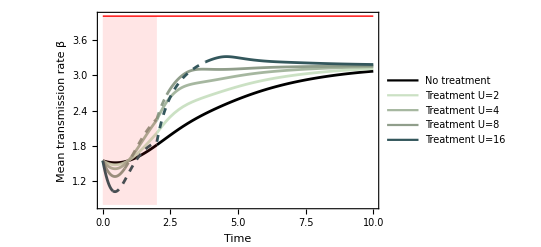

/Users/martin/Documents/lethal/figures/treatment/treatment_chronic_beta_bstart07.pdf

InterpolatingFunction::dmval: Input value {297} lies outside the range of data in the interpolating function. Extrapolation will be used.

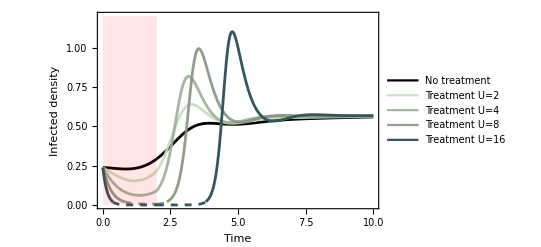

/Users/martin/Documents/lethal/figures/treatment/treatment_chronic_I_bstart07.pdf

InterpolatingFunction::dmval: Input value {3} lies outside the range of data in the interpolating function. Extrapolation will be used.

{0.00936559}

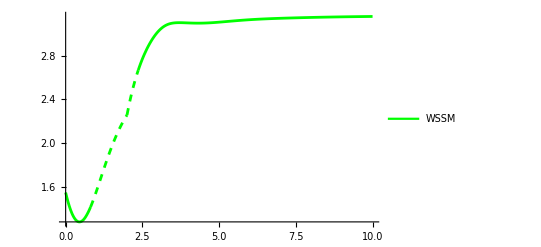

```mathematica
paramsall = {Subscript[β, max] -> 4, α -> 2, θ -> 5, b -> 3, d -> 1,  Vs -> 1,f->0.4, λ->0.05}

ϵ=0.02
t1=0  (*Start treatment*)
t2=2 (*stop treatment*)
t3=10

betastart=4-5*0.7^2
i0=b/(d+α+U*f)-d/betastart/.paramsall/.U->1
s0=(d+α+U f)/betastart/.paramsall /.U->1
U=.
temps=3
f=.
λ=.

init0={Subscript[β, m][0]==OverBar[β0]+(θ σ0)/Vs,σ[0]==σ0,𝒮[0]==b/d,ℐ[0]==1}/.{OverBar[β0]->betastart,σ0->0}/.paramsall;
sol0:=NDSolve[ft[{ODEansatzfull /. U-> 1,init0}]//.paramsall,varsol,{t,0,1*100}];
init={Subscript[β, m][0]==OverBar[β0]+(θ σ0)/Vs,σ[0]==σ0,𝒮[0]==s0,ℐ[0]==i0}/.{OverBar[β0]->betastart,σ0->0}/.paramsall;
sol1:=NDSolve[ft[{ODEansatzfull /. U-> 1,init}]//.paramsall,varsol,{t,0,t2-t1}];
sol2:=NDSolve[ft[{ODEansatzfull /. U-> 2,init}]//.paramsall,varsol,{t,0,t2-t1}];
sol3:=NDSolve[ft[{ODEansatzfull /. U-> 4,init}]//.paramsall,varsol,{t,0,t2-t1}];
sol4:=NDSolve[ft[{ODEansatzfull /. U-> 8,init}]//.paramsall,varsol,{t,0,t2-t1}];
sol5:=NDSolve[ft[{ODEansatzfull /. U->16,init}]//.paramsall,varsol,{t,0,t2-t1}];



pt1=ListPlot[{{t1,0},{t1,4}}, Joined->True, PlotStyle->Black];
pt2=ListPlot[{{t2,0},{t2,4}}, Joined->True, PlotStyle->Red];
ll = Graphics[{Red,Line[{{0,4},{t3,4}}]}];
rectraitement=Graphics[{Opacity[0.1,Red],Rectangle[{t1,0.8},{t2,4.0}]}];
text0 = Graphics[Text[Style["β_0",13,Red],{-0.9,3.96}]];


sol11 = NDSolve[ft[{ODEansatzfull /. U-> 1,{Subscript[β, m][0]==Subscript[β, m][t]/.sol1/.t->t2-t1,σ[0]==σ[t]/.sol1/.t->t2-t1,𝒮[0]==𝒮[t]/.sol1/.t->t2-t1,ℐ[0]==ℐ[t]/.sol1/.t->t2-t1}/.paramsall}]//.paramsall,varsol,{t,0,t3-t2}];
sol22 = NDSolve[ft[{ODEansatzfull /. U-> 1,{Subscript[β, m][0]==Subscript[β, m][t]/.sol2/.t->t2-t1,σ[0]==σ[t]/.sol2/.t->t2-t1,𝒮[0]==𝒮[t]/.sol2/.t->t2-t1,ℐ[0]==ℐ[t]/.sol2/.t->t2-t1}/.paramsall}]//.paramsall,varsol,{t,0,t3-t2}];
sol33 = NDSolve[ft[{ODEansatzfull /. U-> 1,{Subscript[β, m][0]==Subscript[β, m][t]/.sol3/.t->t2-t1,σ[0]==σ[t]/.sol3/.t->t2-t1,𝒮[0]==𝒮[t]/.sol3/.t->t2-t1,ℐ[0]==ℐ[t]/.sol3/.t->t2-t1}/.paramsall}]//.paramsall,varsol,{t,0,t3-t2}];
sol44 = NDSolve[ft[{ODEansatzfull /. U-> 1,{Subscript[β, m][0]==Subscript[β, m][t]/.sol4/.t->t2-t1,σ[0]==σ[t]/.sol4/.t->t2-t1,𝒮[0]==𝒮[t]/.sol4/.t->t2-t1,ℐ[0]==ℐ[t]/.sol4/.t->t2-t1}/.paramsall}]//.paramsall,varsol,{t,0,t3-t2}];
sol55 = NDSolve[ft[{ODEansatzfull /. U-> 1,{Subscript[β, m][0]==Subscript[β, m][t]/.sol5/.t->t2-t1,σ[0]==σ[t]/.sol5/.t->t2-t1,𝒮[0]==𝒮[t]/.sol5/.t->t2-t1,ℐ[0]==ℐ[t]/.sol5/.t->t2-t1}/.paramsall}]//.paramsall,varsol,{t,0,t3-t2}];



pbbaru0=Plot[Evaluate[2/.sol0/.t->x/.paramsall],{x,0,1},PlotRange->{{0,t1},{1.5,3}},PlotStyle->{Dashed,Gray}];
pbbaru1=Plot[If[First[Evaluate[ℐ[t]/.sol1/.t->x-t1/.paramsall]]>ϵ,First[Evaluate[(Subscript[β, m][t]-(θ σ[t])/Vs)/.sol1/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotLegends->LineLegend[{Black},{"No treatment"}], PlotStyle->Black];
pbbaru1bis=Plot[If[First[Evaluate[ℐ[t]/.sol1/.t->x-t1/.paramsall]]<ϵ,First[Evaluate[(Subscript[β, m][t]-(θ σ[t])/Vs)/.sol1/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotStyle->{Dashed,c0}];
pbbaru2=Plot[If[First[Evaluate[ℐ[t]/.sol2/.t->x-t1/.paramsall]]>ϵ,First[Evaluate[(Subscript[β, m][t]-(θ σ[t])/Vs)/.sol2/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotLegends->LineLegend[{c1},{"Treatment U=2"}],PlotStyle->c1];
pbbaru2bis=Plot[If[First[Evaluate[ℐ[t]/.sol2/.t->x-t1/.paramsall]]<ϵ,First[Evaluate[(Subscript[β, m][t]-(θ σ[t])/Vs)/.sol2/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotStyle->{Dashed,c1}];
pbbaru3=Plot[If[First[Evaluate[ℐ[t]/.sol3/.t->x-t1/.paramsall]]>ϵ,First[Evaluate[(Subscript[β, m][t]-(θ σ[t])/Vs)/.sol3/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotLegends->LineLegend[{c2},{"Treatment U=4"}],PlotStyle->c2];
pbbaru3bis=Plot[If[First[Evaluate[ℐ[t]/.sol3/.t->x-t1/.paramsall]]<ϵ,First[Evaluate[(Subscript[β, m][t]-(θ σ[t])/Vs)/.sol3/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotStyle->{Dashed,c2}];
pbbaru4=Plot[If[First[Evaluate[ℐ[t]/.sol4/.t->x-t1/.paramsall]]>ϵ,First[Evaluate[(Subscript[β, m][t]-(θ σ[t])/Vs)/.sol4/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotLegends->LineLegend[{c3},{"Treatment U=8"}],PlotStyle->c3];
pbbaru4bis=Plot[If[First[Evaluate[ℐ[t]/.sol4/.t->x-t1/.paramsall]]<ϵ,First[Evaluate[(Subscript[β, m][t]-(θ σ[t])/Vs)/.sol4/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotStyle->{Dashed,c3}];

pbbaru5=Plot[If[First[Evaluate[ℐ[t]/.sol5/.t->x-t1/.paramsall]]>ϵ,First[Evaluate[(Subscript[β, m][t]-(θ σ[t])/Vs)/.sol5/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotLegends->LineLegend[{c4},{"Treatment U=16"}],PlotStyle->c4];
pbbaru5bis=Plot[If[First[Evaluate[ℐ[t]/.sol5/.t->x-t1/.paramsall]]<ϵ,First[Evaluate[(Subscript[β, m][t]-(θ σ[t])/Vs)/.sol5/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotStyle->{Dashed,c4}];



pbbaru11=Plot[If[First[Evaluate[ℐ[t]/.sol11/.t->x-t2/.paramsall]]>ϵ,Evaluate[(Subscript[β, m][t]-(θ σ[t])/Vs)/.sol11/.t->x-t2/.paramsall],None],{x,t2,t3},PlotRange->All, PlotStyle->{Black}];
pbbaru11bis=Plot[If[First[Evaluate[ℐ[t]/.sol11/.t->x-t2/.paramsall]]<ϵ,Evaluate[(Subscript[β, m][t]-(θ σ[t])/Vs)/.sol11/.t->x-t2/.paramsall],None],{x,t2,t3},PlotRange->All, PlotStyle->{Dashed,c0}];
pbbaru22=Plot[If[First[Evaluate[ℐ[t]/.sol22/.t->x-t2/.paramsall]]>ϵ,Evaluate[(Subscript[β, m][t]-(θ σ[t])/Vs)/.sol22/.t->x-t2/.paramsall],None],{x,t2,t3},PlotRange->All, PlotStyle->{c1}];
pbbaru22bis=Plot[If[First[Evaluate[ℐ[t]/.sol22/.t->x-t2/.paramsall]]<ϵ,Evaluate[(Subscript[β, m][t]-(θ σ[t])/Vs)/.sol22/.t->x-t2/.paramsall],None],{x,t2,t3},PlotRange->All, PlotStyle->{Dashed,c1}];
pbbaru33=Plot[If[First[Evaluate[ℐ[t]/.sol33/.t->x-t2/.paramsall]]>ϵ,Evaluate[(Subscript[β, m][t]-(θ σ[t])/Vs)/.sol33/.t->x-t2/.paramsall],None],{x,t2,t3},PlotRange->All, PlotStyle->{c2}];
pbbaru33bis=Plot[If[First[Evaluate[ℐ[t]/.sol33/.t->x-t2/.paramsall]]<ϵ,Evaluate[(Subscript[β, m][t]-(θ σ[t])/Vs)/.sol33/.t->x-t2/.paramsall],None],{x,t2,t3},PlotRange->All, PlotStyle->{Dashed,c2}];
pbbaru44=Plot[If[First[Evaluate[ℐ[t]/.sol44/.t->x-t2/.paramsall]]>ϵ,Evaluate[(Subscript[β, m][t]-(θ σ[t])/Vs)/.sol44/.t->x-t2/.paramsall],None],{x,t2,t3},PlotRange->All, PlotStyle->{c3}];
pbbaru44bis=Plot[If[First[Evaluate[ℐ[t]/.sol44/.t->x-t2/.paramsall]]<ϵ,Evaluate[(Subscript[β, m][t]-(θ σ[t])/Vs)/.sol44/.t->x-t2/.paramsall],None],{x,t2,t3},PlotRange->All, PlotStyle->{Dashed,c3}];
pbbaru55=Plot[If[First[Evaluate[ℐ[t]/.sol55/.t->x-t2/.paramsall]]>ϵ,Evaluate[(Subscript[β, m][t]-(θ σ[t])/Vs)/.sol55/.t->x-t2/.paramsall],None],{x,t2,t3},PlotRange->All, PlotStyle->{c4}];
pbbaru55bis=Plot[If[First[Evaluate[ℐ[t]/.sol55/.t->x-t2/.paramsall]]<ϵ,Evaluate[(Subscript[β, m][t]-(θ σ[t])/Vs)/.sol55/.t->x-t2/.paramsall],None],{x,t2,t3},PlotRange->All, PlotStyle->{Dashed,c4}];

Show[pbbaru1,pbbaru2,pbbaru3,pbbaru1bis,pbbaru2bis,pbbaru3bis,pbbaru4,pbbaru4bis,pbbaru5,pbbaru5bis,pbbaru11,pbbaru22,pbbaru33,pbbaru11bis,pbbaru22bis,pbbaru33bis,pbbaru44,pbbaru44bis,pbbaru55,pbbaru55bis, ll,rectraitement,text0,Frame->{True,True,False,True},FrameStyle->{Black,Black,Automatic,Black}, FrameLabel->{Style["Time",16],Style["Mean transmission rate β̄",14]}, PlotRange->{{0,t3},{0.8,4}},PlotRangePadding->0, AxesOrigin->{0,1.1}, PlotRangeClipping->False, ImagePadding->50]

Export["/Users/martin/Documents/lethal/figures/treatment/treatment_chronic_beta_bstart07.pdf",%]



piu0=Plot[Evaluate[ℐ[t]/.sol0/.t->temps*99],{x,0,1},PlotRange->All,PlotStyle->{Dashed,Gray}];
piu1=Plot[If[First[Evaluate[ℐ[t]/.sol1/.t->x-t1/.paramsall]]>ϵ,First[Evaluate[ℐ[t]/.sol1/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->{{0,t3},{0,10}},PlotLegends->LineLegend[{Black},{"No treatment"}], PlotStyle->Black];
piu1bis=Plot[If[First[Evaluate[ℐ[t]/.sol1/.t->x-t1/.paramsall]]<ϵ,First[Evaluate[ℐ[t]/.sol1/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All, PlotStyle->{Dashed,c0}];
piu2=Plot[If[First[Evaluate[ℐ[t]/.sol2/.t->x-t1/.paramsall]]>ϵ,First[Evaluate[ℐ[t]/.sol2/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotLegends->LineLegend[{c1},{"Treatment U=2"}],PlotStyle->c1];
piu2bis=Plot[If[First[Evaluate[ℐ[t]/.sol2/.t->x-t1/.paramsall]]<ϵ,First[Evaluate[ℐ[t]/.sol2/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All, PlotStyle->{Dashed,c1}];
piu3=Plot[If[First[Evaluate[ℐ[t]/.sol3/.t->x-t1/.paramsall]]>ϵ,First[Evaluate[ℐ[t]/.sol3/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotLegends->LineLegend[{c2},{"Treatment U=4"}],PlotStyle->c2];
piu3bis=Plot[If[First[Evaluate[ℐ[t]/.sol3/.t->x-t1/.paramsall]]<ϵ,First[Evaluate[ℐ[t]/.sol3/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All, PlotStyle->{Dashed,c2}];
piu4=Plot[If[First[Evaluate[ℐ[t]/.sol4/.t->x-t1/.paramsall]]>ϵ,First[Evaluate[ℐ[t]/.sol4/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotLegends->LineLegend[{c3},{"Treatment U=8"}],PlotStyle->c3];
piu4bis=Plot[If[First[Evaluate[ℐ[t]/.sol4/.t->x-t1/.paramsall]]<ϵ,First[Evaluate[ℐ[t]/.sol4/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All, PlotStyle->{Dashed,c3}];
piu5=Plot[If[First[Evaluate[ℐ[t]/.sol5/.t->x-t1/.paramsall]]>ϵ,First[Evaluate[ℐ[t]/.sol5/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotLegends->LineLegend[{c4},{"Treatment U=16"}],PlotStyle->c4];
piu5bis=Plot[If[First[Evaluate[ℐ[t]/.sol5/.t->x-t1/.paramsall]]<ϵ,First[Evaluate[ℐ[t]/.sol5/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All, PlotStyle->{Dashed,c4}];

piu11=Plot[If[First[Evaluate[ℐ[t]/.sol11/.t->x-t2/.paramsall]]>ϵ,First[Evaluate[ℐ[t]/.sol11/.t->x-t2/.paramsall]],None],{x,t2,t3},PlotRange->{{0,t3},{0,10}}, PlotStyle->{Black}];
piu11bis=Plot[If[First[Evaluate[ℐ[t]/.sol11/.t->x-t2/.paramsall]]<ϵ,First[Evaluate[ℐ[t]/.sol11/.t->x-t2/.paramsall]],None],{x,t2,t3},PlotRange->All, PlotStyle->{Black,c0}];
piu22=Plot[If[First[Evaluate[ℐ[t]/.sol22/.t->x-t2/.paramsall]]>ϵ,First[Evaluate[ℐ[t]/.sol22/.t->x-t2/.paramsall]],None],{x,t2,t3},PlotRange->All, PlotStyle->{c1}];
piu22bis=Plot[If[First[Evaluate[ℐ[t]/.sol22/.t->x-t2/.paramsall]]<ϵ,First[Evaluate[ℐ[t]/.sol22/.t->x-t2/.paramsall]],None],{x,t2,t3},PlotRange->All, PlotStyle->{Dashed,c1}];
piu33=Plot[If[First[Evaluate[ℐ[t]/.sol33/.t->x-t2/.paramsall]]>ϵ,First[Evaluate[ℐ[t]/.sol33/.t->x-t2/.paramsall]],None],{x,t2,t3},PlotRange->All, PlotStyle->{c2}];
piu33bis=Plot[If[First[Evaluate[ℐ[t]/.sol33/.t->x-t2/.paramsall]]<ϵ,First[Evaluate[ℐ[t]/.sol33/.t->x-t2/.paramsall]],None],{x,t2,t3},PlotRange->All, PlotStyle->{Dashed,c2}];
piu44=Plot[If[First[Evaluate[ℐ[t]/.sol44/.t->x-t2/.paramsall]]>ϵ,First[Evaluate[ℐ[t]/.sol44/.t->x-t2/.paramsall]],None],{x,t2,t3},PlotRange->All, PlotStyle->{c3}];
piu44bis=Plot[If[First[Evaluate[ℐ[t]/.sol44/.t->x-t2/.paramsall]]<ϵ,First[Evaluate[ℐ[t]/.sol44/.t->x-t2/.paramsall]],None],{x,t2,t3},PlotRange->All, PlotStyle->{Dashed,c3}];
piu55=Plot[If[First[Evaluate[ℐ[t]/.sol55/.t->x-t2/.paramsall]]>ϵ,First[Evaluate[ℐ[t]/.sol55/.t->x-t2/.paramsall]],None],{x,t2,t3},PlotRange->All, PlotStyle->{c4}];
piu55bis=Plot[If[First[Evaluate[ℐ[t]/.sol55/.t->x-t2/.paramsall]]<ϵ,First[Evaluate[ℐ[t]/.sol55/.t->x-t2/.paramsall]],None],{x,t2,t3},PlotRange->All, PlotStyle->{Dashed,c4}];
rectraitement=Graphics[{Opacity[0.1,Red],Rectangle[{t1,0},{t2,1.2}]}];


Show[piu1,piu2,piu3,piu4,piu5,piu4bis,piu5bis,piu11,piu22,piu33,piu44,piu44bis,piu55,piu55bis,rectraitement, Frame->{True,True,True,True},FrameStyle->{Black,Black,Black,Black}, FrameLabel->{Style["Time",16],Style["Infected density",15]}, PlotRange->{{0,t3},{0,1.2}},PlotRangePadding->0, ImagePadding->50]
Export["/Users/martin/Documents/lethal/figures/treatment/treatment_chronic_I_bstart07.pdf",%]
Evaluate[ℐ[t]/.sol4/.t->temps/.paramsall]


pbbaru4=Plot[If[First[Evaluate[ℐ[t]/.sol4/.t->x-t1/.paramsall]]>ϵ,First[Evaluate[(Subscript[β, m][t]-(θ σ[t])/Vs)/.sol4/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotLegends->LineLegend[{Green},{"WSSM"}],PlotStyle->Green];
pbbaru4bis=Plot[If[First[Evaluate[ℐ[t]/.sol4/.t->x-t1/.paramsall]]<ϵ,First[Evaluate[(Subscript[β, m][t]-(θ σ[t])/Vs)/.sol4/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotStyle->{Dashed,Green}];

pbbaru44=Plot[If[First[Evaluate[ℐ[t]/.sol44/.t->x-t2/.paramsall]]>ϵ,Evaluate[(Subscript[β, m][t]-(θ σ[t])/Vs)/.sol44/.t->x-t2/.paramsall],None],{x,t2,t3},PlotRange->All, PlotStyle->{Green}];
pbbaru44bis=Plot[If[First[Evaluate[ℐ[t]/.sol44/.t->x-t2/.paramsall]]<ϵ,Evaluate[(Subscript[β, m][t]-(θ σ[t])/Vs)/.sol44/.t->x-t2/.paramsall],None],{x,t2,t3},PlotRange->All, PlotStyle->{Dashed,Green}];

x=Show[pbbaru4,pbbaru4bis,pbbaru44,pbbaru44bis, PlotRange->All]
```

```mathematica
σtest= (√d √Vs Sqrt[U(1-f) λ])/(√b);
soluc=Solve[ ((Subscript[β, max]-(θ σ)/Vs)*b/d- (d + α + U f) /.σ->σtest)==0,U];
soluc /.{Subscript[β, max] -> 4, α -> 4, θ -> 1, b -> 2, d -> 1, Vs -> 2,f->0.4,λ->0.05}
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{U→6.4042},{U→8.7833}}

```mathematica
soluc/.Vs->1/Subscript[s, β]/.θ->n/2//fs
```

{{U→-(b (-1+f) n^2 λ s_β-8 b f β_max+d (8 f (d+α)+√((b (-1+f) n^2 λ s_β (16 d f (d+α)+b (-1+f) n^2 λ s_β-16 b f β_max))/d^2)))/(8 d f^2)},{U→(-b (-1+f) n^2 λ s_β+8 b f β_max+d (-8 f (d+α)+√((b (-1+f) n^2 λ s_β (16 d f (d+α)+b (-1+f) n^2 λ s_β-16 b f β_max))/d^2)))/(8 d f^2)}}

#### Mutagenic treatment ACUTE

colors

```mathematica
hexToRGB=RGBColor@@(IntegerDigits[#~StringDrop~1~FromDigits~16,256,3]/255.)&

x0=1.2
x1=1.05
x2=0.83
x3=0.7

c0=Opacity[0.9,RGBColor[0.74*x0,0.83*x0,0.711*x0]]
c1=Opacity[0.9,RGBColor[0.74*x1,0.83*x1,0.711*x1]]
c2=Opacity[0.9,RGBColor[0.74*x2,0.83*x2,0.711*x2]]
c3=Opacity[0.9,RGBColor[0.74*x3,0.83*x3,0.711*x3]]
c4=RGBColor[0.2,0.34,0.36]
```

RGBColor@@IntegerDigits[FromDigits[StringDrop[#1,1],16],256,3]/255.&

1.2

1.05

0.83

0.7

Opacity[0.9,RGBColor[0.888, 0.9959999999999999, 0.8532]]

Opacity[0.9,RGBColor[0.777, 0.8714999999999999, 0.74655]]

Opacity[0.9,RGBColor[0.6142, 0.6889, 0.5901299999999999]]

Opacity[0.9,RGBColor[0.518, 0.581, 0.4976999999999999]]

RGBColor[0.2, 0.34, 0.36]

0

2

3

4 α

3.2

0.569853

1.0625

{β_max→4,α→2,θ→5,b→3,d→1,α→1,Vs→1,f→0.4,λ→0.05}

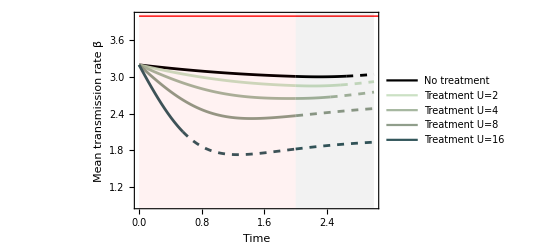

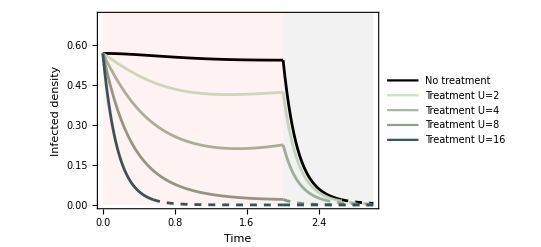

InterpolatingFunction::dmval: Input value {3} lies outside the range of data in the interpolating function. Extrapolation will be used.

{0.0214678}

```mathematica
t1=0  (*Start treatment, start acute, α -> αacute*)
t2=2(*stop treatment*)
t3=3

αacute=4 α

betastart=4-5*0.4^2


i0=b/(d+α+U*f)-d/betastart/.paramsall/.U->1
s0=(d+α+U f)/betastart/.paramsall /.U->1

paramsall = {Subscript[β, max] -> 4, α -> 2, θ -> 5, b -> 3, d -> 1, α -> 1, Vs -> 1,f->0.4, λ->0.05}
init0={Subscript[β, m][0]==OverBar[β0]+(θ σ0)/Vs,σ[0]==σ0,𝒮[0]==b/d,ℐ[0]==1}/.{OverBar[β0]->betastart,σ0->0}/.paramsall;
sol0:=NDSolve[ft[{ODEansatzfull /. U-> 1,init0}]//.paramsall,varsol,{t,0,temps*100}];
init={Subscript[β, m][0]==OverBar[β0]+(θ σ0)/Vs,σ[0]==σ0,𝒮[0]==s0,ℐ[0]==i0}/.{OverBar[β0]->betastart,σ0->0}/.paramsall;
sol1:=NDSolve[ft[{ODEansatzfull /. U-> 1,init}]//.paramsall,varsol,{t,0,t2-t1}];
sol2:=NDSolve[ft[{ODEansatzfull /. U-> 2,init}]//.paramsall,varsol,{t,0,t2-t1}];
sol3:=NDSolve[ft[{ODEansatzfull /. U-> 4,init}]//.paramsall,varsol,{t,0,t2-t1}];
sol4:=NDSolve[ft[{ODEansatzfull/. U-> 8,init}]//.paramsall,varsol,{t,0,t2-t1}];
sol5:=NDSolve[ft[{ODEansatzfull /. U->16,init}]//.paramsall,varsol,{t,0,t2-t1}];

pt1=ListPlot[{{t1,0},{t1,4}}, Joined->True, PlotStyle->Black];
pt2=ListPlot[{{t2,0},{t2,4}}, Joined->True, PlotStyle->Red];
rectraitement=Graphics[{Opacity[0.05,Red],Rectangle[{t1,0},{t2,100}]}];
recacute=Graphics[{Opacity[0.05,Black],Rectangle[{t2,0},{t3,100}]}];
text0 = Graphics[Text[Style["β_0",13,Red],{-0.9,3.96}]];

sol11 = NDSolve[ft[{ODEansatzfull /.α->αacute/. U-> 1,{Subscript[β, m][0]==Subscript[β, m][t]/.sol1/.t->t2-t1,σ[0]==σ[t]/.sol1/.t->t2-t1,𝒮[0]==𝒮[t]/.sol1/.t->t2-t1,ℐ[0]==ℐ[t]/.sol1/.t->t2-t1}/.paramsall}]//.paramsall,varsol,{t,0,t3-t2}];
sol22 = NDSolve[ft[{ODEansatzfull /.α->αacute/. U-> 2,{Subscript[β, m][0]==Subscript[β, m][t]/.sol2/.t->t2-t1,σ[0]==σ[t]/.sol2/.t->t2-t1,𝒮[0]==𝒮[t]/.sol2/.t->t2-t1,ℐ[0]==ℐ[t]/.sol2/.t->t2-t1}/.paramsall}]//.paramsall,varsol,{t,0,t3-t2}];
sol33 = NDSolve[ft[{ODEansatzfull /.α->αacute/. U-> 4,{Subscript[β, m][0]==Subscript[β, m][t]/.sol3/.t->t2-t1,σ[0]==σ[t]/.sol3/.t->t2-t1,𝒮[0]==𝒮[t]/.sol3/.t->t2-t1,ℐ[0]==ℐ[t]/.sol3/.t->t2-t1}/.paramsall}]//.paramsall,varsol,{t,0,t3-t2}];
sol44 = NDSolve[ft[{ODEansatzfull /.α->αacute/. U-> 8,{Subscript[β, m][0]==Subscript[β, m][t]/.sol4/.t->t2-t1,σ[0]==σ[t]/.sol4/.t->t2-t1,𝒮[0]==𝒮[t]/.sol4/.t->t2-t1,ℐ[0]==ℐ[t]/.sol4/.t->t2-t1}/.paramsall}]//.paramsall,varsol,{t,0,t3-t2}];
sol55 = NDSolve[ft[{ODEansatzfull /.α->αacute/. U-> 16,{Subscript[β, m][0]==Subscript[β, m][t]/.sol5/.t->t2-t1,σ[0]==σ[t]/.sol5/.t->t2-t1,𝒮[0]==𝒮[t]/.sol5/.t->t2-t1,ℐ[0]==ℐ[t]/.sol5/.t->t2-t1}/.paramsall}]//.paramsall,varsol,{t,0,t3-t2}];


(*
sol11 = NDSolve[ft[{ODEansatzfull /.α->αacute/. U-> 1,{Subscript[β, m][0]==Subscript[β, m][t]/.sol1/.t->t2-t1,σ[0]==σ[t]/.sol1/.t->t2-t1,𝒮[0]==𝒮[t]/.sol1/.t->t2-t1,ℐ[0]==ℐ[t]/.sol1/.t->t2-t1}/.paramsall}]//.paramsall,varsol,{t,0,t3-t2}];
sol22 = NDSolve[ft[{ODEansatzfull /.α->αacute/. U-> 1,{Subscript[β, m][0]==Subscript[β, m][t]/.sol2/.t->t2-t1,σ[0]==σ[t]/.sol2/.t->t2-t1,𝒮[0]==𝒮[t]/.sol2/.t->t2-t1,ℐ[0]==ℐ[t]/.sol2/.t->t2-t1}/.paramsall}]//.paramsall,varsol,{t,0,t3-t2}];
sol33 = NDSolve[ft[{ODEansatzfull /.α->αacute/. U-> 1,{Subscript[β, m][0]==Subscript[β, m][t]/.sol3/.t->t2-t1,σ[0]==σ[t]/.sol3/.t->t2-t1,𝒮[0]==𝒮[t]/.sol3/.t->t2-t1,ℐ[0]==ℐ[t]/.sol3/.t->t2-t1}/.paramsall}]//.paramsall,varsol,{t,0,t3-t2}];
sol44 = NDSolve[ft[{ODEansatzfull /.α->αacute/. U-> 1,{Subscript[β, m][0]==Subscript[β, m][t]/.sol4/.t->t2-t1,σ[0]==σ[t]/.sol4/.t->t2-t1,𝒮[0]==𝒮[t]/.sol4/.t->t2-t1,ℐ[0]==ℐ[t]/.sol4/.t->t2-t1}/.paramsall}]//.paramsall,varsol,{t,0,t3-t2}];
sol55 = NDSolve[ft[{ODEansatzfull /.α->αacute/. U-> 1,{Subscript[β, m][0]==Subscript[β, m][t]/.sol5/.t->t2-t1,σ[0]==σ[t]/.sol5/.t->t2-t1,𝒮[0]==𝒮[t]/.sol5/.t->t2-t1,ℐ[0]==ℐ[t]/.sol5/.t->t2-t1}/.paramsall}]//.paramsall,varsol,{t,0,t3-t2}];*)


pbbaru0=Plot[Evaluate[2/.sol0/.t->x/.paramsall],{x,0,1},PlotRange->{{0,t1},{1.5,3}},PlotStyle->{Dashed,Gray}];
pbbaru1=Plot[If[First[Evaluate[ℐ[t]/.sol1/.t->x-t1/.paramsall]]>ϵ,First[Evaluate[(Subscript[β, m][t]-(θ σ[t])/Vs)/.sol1/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotLegends->LineLegend[{Black},{"No treatment"}], PlotStyle->Black];
pbbaru1bis=Plot[If[First[Evaluate[ℐ[t]/.sol1/.t->x-t1/.paramsall]]<ϵ,First[Evaluate[(Subscript[β, m][t]-(θ σ[t])/Vs)/.sol1/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotStyle->{Dashed,Black}];
pbbaru2=Plot[If[First[Evaluate[ℐ[t]/.sol2/.t->x-t1/.paramsall]]>ϵ,First[Evaluate[(Subscript[β, m][t]-(θ σ[t])/Vs)/.sol2/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotLegends->LineLegend[{c1},{"Treatment U=2"}],PlotStyle->c1];
pbbaru2bis=Plot[If[First[Evaluate[ℐ[t]/.sol2/.t->x-t1/.paramsall]]<ϵ,First[Evaluate[(Subscript[β, m][t]-(θ σ[t])/Vs)/.sol2/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotStyle->{Dashed,c1}];
pbbaru3=Plot[If[First[Evaluate[ℐ[t]/.sol3/.t->x-t1/.paramsall]]>ϵ,First[Evaluate[(Subscript[β, m][t]-(θ σ[t])/Vs)/.sol3/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotLegends->LineLegend[{c2},{"Treatment U=4"}],PlotStyle->c2];
pbbaru3bis=Plot[If[First[Evaluate[ℐ[t]/.sol3/.t->x-t1/.paramsall]]<ϵ,First[Evaluate[(Subscript[β, m][t]-(θ σ[t])/Vs)/.sol3/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotStyle->{Dashed,c2}];
pbbaru4=Plot[If[First[Evaluate[ℐ[t]/.sol4/.t->x-t1/.paramsall]]>ϵ,First[Evaluate[(Subscript[β, m][t]-(θ σ[t])/Vs)/.sol4/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotLegends->LineLegend[{c3},{"Treatment U=8"}],PlotStyle->c3];
pbbaru4bis=Plot[If[First[Evaluate[ℐ[t]/.sol4/.t->x-t1/.paramsall]]<ϵ,First[Evaluate[(Subscript[β, m][t]-(θ σ[t])/Vs)/.sol4/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotStyle->{Dashed,c3}];

pbbaru5=Plot[If[First[Evaluate[ℐ[t]/.sol5/.t->x-t1/.paramsall]]>ϵ,First[Evaluate[(Subscript[β, m][t]-(θ σ[t])/Vs)/.sol5/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotLegends->LineLegend[{c4},{"Treatment U=16"}],PlotStyle->c4];
pbbaru5bis=Plot[If[First[Evaluate[ℐ[t]/.sol5/.t->x-t1/.paramsall]]<ϵ,First[Evaluate[(Subscript[β, m][t]-(θ σ[t])/Vs)/.sol5/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotStyle->{Dashed,c4}];



pbbaru11=Plot[If[First[Evaluate[ℐ[t]/.sol11/.t->x-t2/.paramsall]]>ϵ,Evaluate[(Subscript[β, m][t]-(θ σ[t])/Vs)/.sol11/.t->x-t2/.paramsall],None],{x,t2,t3},PlotRange->All, PlotStyle->{Black}];
pbbaru11bis=Plot[If[First[Evaluate[ℐ[t]/.sol11/.t->x-t2/.paramsall]]<ϵ,Evaluate[(Subscript[β, m][t]-(θ σ[t])/Vs)/.sol11/.t->x-t2/.paramsall],None],{x,t2,t3},PlotRange->All, PlotStyle->{Dashed,Black}];
pbbaru22=Plot[If[First[Evaluate[ℐ[t]/.sol22/.t->x-t2/.paramsall]]>ϵ,Evaluate[(Subscript[β, m][t]-(θ σ[t])/Vs)/.sol22/.t->x-t2/.paramsall],None],{x,t2,t3},PlotRange->All, PlotStyle->{c1}];
pbbaru22bis=Plot[If[First[Evaluate[ℐ[t]/.sol22/.t->x-t2/.paramsall]]<ϵ,Evaluate[(Subscript[β, m][t]-(θ σ[t])/Vs)/.sol22/.t->x-t2/.paramsall],None],{x,t2,t3},PlotRange->All, PlotStyle->{Dashed,c1}];
pbbaru33=Plot[If[First[Evaluate[ℐ[t]/.sol33/.t->x-t2/.paramsall]]>ϵ,Evaluate[(Subscript[β, m][t]-(θ σ[t])/Vs)/.sol33/.t->x-t2/.paramsall],None],{x,t2,t3},PlotRange->All, PlotStyle->{c2}];
pbbaru33bis=Plot[If[First[Evaluate[ℐ[t]/.sol33/.t->x-t2/.paramsall]]<ϵ,Evaluate[(Subscript[β, m][t]-(θ σ[t])/Vs)/.sol33/.t->x-t2/.paramsall],None],{x,t2,t3},PlotRange->All, PlotStyle->{Dashed,c2}];
pbbaru44=Plot[If[First[Evaluate[ℐ[t]/.sol44/.t->x-t2/.paramsall]]>ϵ,Evaluate[(Subscript[β, m][t]-(θ σ[t])/Vs)/.sol44/.t->x-t2/.paramsall],None],{x,t2,t3},PlotRange->All, PlotStyle->{c3}];
pbbaru44bis=Plot[If[First[Evaluate[ℐ[t]/.sol44/.t->x-t2/.paramsall]]<ϵ,Evaluate[(Subscript[β, m][t]-(θ σ[t])/Vs)/.sol44/.t->x-t2/.paramsall],None],{x,t2,t3},PlotRange->All, PlotStyle->{Dashed,c3}];
pbbaru55=Plot[If[First[Evaluate[ℐ[t]/.sol55/.t->x-t2/.paramsall]]>ϵ,Evaluate[(Subscript[β, m][t]-(θ σ[t])/Vs)/.sol55/.t->x-t2/.paramsall],None],{x,t2,t3},PlotRange->All, PlotStyle->{c4}];
pbbaru55bis=Plot[If[First[Evaluate[ℐ[t]/.sol55/.t->x-t2/.paramsall]]<ϵ,Evaluate[(Subscript[β, m][t]-(θ σ[t])/Vs)/.sol55/.t->x-t2/.paramsall],None],{x,t2,t3},PlotRange->All, PlotStyle->{Dashed,c4}];

Show[pbbaru1,pbbaru2,pbbaru3,pbbaru1bis,pbbaru2bis,pbbaru3bis,pbbaru4,pbbaru4bis,pbbaru5,pbbaru5bis,pbbaru11,pbbaru22,pbbaru33,pbbaru11bis,pbbaru22bis,pbbaru33bis,pbbaru44,pbbaru44bis,pbbaru55,pbbaru55bis, ll,rectraitement,recacute,text0,Frame->{True,True,False,True},FrameStyle->{Black,Black,Automatic,Black}, FrameLabel->{Style["Time",16],Style["Mean transmission rate β̄",14]}, PlotRange->{{0,t3},{0.9,4}},PlotRangePadding->0, AxesOrigin->{0,1.1}, ImagePadding->50]

(*Export["/Users/martin/Documents/lethal/figures/treatment/treatment_acute_beta_bstart04.pdf",%]*)


piu0=Plot[Evaluate[ℐ[t]/.sol0/.t->temps*99],{x,0,1},PlotRange->All,PlotStyle->{Dashed,Gray}];
piu1=Plot[If[First[Evaluate[ℐ[t]/.sol1/.t->x-t1/.paramsall]]>ϵ,First[Evaluate[ℐ[t]/.sol1/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotLegends->LineLegend[{Black},{"No treatment"}], PlotStyle->Black];
piu1bis=Plot[If[First[Evaluate[ℐ[t]/.sol1/.t->x-t1/.paramsall]]<ϵ,First[Evaluate[ℐ[t]/.sol1/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All, PlotStyle->{Dashed,Black}];
piu2=Plot[If[First[Evaluate[ℐ[t]/.sol2/.t->x-t1/.paramsall]]>ϵ,First[Evaluate[ℐ[t]/.sol2/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotLegends->LineLegend[{c1},{"Treatment U=2"}],PlotStyle->c1];
piu2bis=Plot[If[First[Evaluate[ℐ[t]/.sol2/.t->x-t1/.paramsall]]<ϵ,First[Evaluate[ℐ[t]/.sol2/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All, PlotStyle->{Dashed,c1}];
piu3=Plot[If[First[Evaluate[ℐ[t]/.sol3/.t->x-t1/.paramsall]]>ϵ,First[Evaluate[ℐ[t]/.sol3/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotLegends->LineLegend[{c2},{"Treatment U=4"}],PlotStyle->c2];
piu3bis=Plot[If[First[Evaluate[ℐ[t]/.sol3/.t->x-t1/.paramsall]]<ϵ,First[Evaluate[ℐ[t]/.sol3/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All, PlotStyle->{Dashed,c2}];
piu4=Plot[If[First[Evaluate[ℐ[t]/.sol4/.t->x-t1/.paramsall]]>ϵ,First[Evaluate[ℐ[t]/.sol4/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotLegends->LineLegend[{c3},{"Treatment U=8"}],PlotStyle->c3];
piu4bis=Plot[If[First[Evaluate[ℐ[t]/.sol4/.t->x-t1/.paramsall]]<ϵ,First[Evaluate[ℐ[t]/.sol4/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All, PlotStyle->{Dashed,c3}];
piu5=Plot[If[First[Evaluate[ℐ[t]/.sol5/.t->x-t1/.paramsall]]>ϵ,First[Evaluate[ℐ[t]/.sol5/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotLegends->LineLegend[{c4},{"Treatment U=16"}],PlotStyle->c4];
piu5bis=Plot[If[First[Evaluate[ℐ[t]/.sol5/.t->x-t1/.paramsall]]<ϵ,First[Evaluate[ℐ[t]/.sol5/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All, PlotStyle->{Dashed,c4}];

piu11=Plot[If[First[Evaluate[ℐ[t]/.sol11/.t->x-t2/.paramsall]]>ϵ,First[Evaluate[ℐ[t]/.sol11/.t->x-t2/.paramsall]],None],{x,t2,t3},PlotRange->All, PlotStyle->{Black}];
piu11bis=Plot[If[First[Evaluate[ℐ[t]/.sol11/.t->x-t2/.paramsall]]<ϵ,First[Evaluate[ℐ[t]/.sol11/.t->x-t2/.paramsall]],None],{x,t2,t3},PlotRange->All, PlotStyle->{Dashed,Black}];
piu22=Plot[If[First[Evaluate[ℐ[t]/.sol22/.t->x-t2/.paramsall]]>ϵ,First[Evaluate[ℐ[t]/.sol22/.t->x-t2/.paramsall]],None],{x,t2,t3},PlotRange->All, PlotStyle->{c1}];
piu22bis=Plot[If[First[Evaluate[ℐ[t]/.sol22/.t->x-t2/.paramsall]]<ϵ,First[Evaluate[ℐ[t]/.sol22/.t->x-t2/.paramsall]],None],{x,t2,t3},PlotRange->All, PlotStyle->{Dashed,c1}];
piu33=Plot[If[First[Evaluate[ℐ[t]/.sol33/.t->x-t2/.paramsall]]>ϵ,First[Evaluate[ℐ[t]/.sol33/.t->x-t2/.paramsall]],None],{x,t2,t3},PlotRange->All, PlotStyle->{c2}];
piu33bis=Plot[If[First[Evaluate[ℐ[t]/.sol33/.t->x-t2/.paramsall]]<ϵ,First[Evaluate[ℐ[t]/.sol33/.t->x-t2/.paramsall]],None],{x,t2,t3},PlotRange->All, PlotStyle->{Dashed,c2}];
piu44=Plot[If[First[Evaluate[ℐ[t]/.sol44/.t->x-t2/.paramsall]]>ϵ,First[Evaluate[ℐ[t]/.sol44/.t->x-t2/.paramsall]],None],{x,t2,t3},PlotRange->All, PlotStyle->{c3}];
piu44bis=Plot[If[First[Evaluate[ℐ[t]/.sol44/.t->x-t2/.paramsall]]<ϵ,First[Evaluate[ℐ[t]/.sol44/.t->x-t2/.paramsall]],None],{x,t2,t3},PlotRange->All, PlotStyle->{Dashed,c3}];
piu55=Plot[If[First[Evaluate[ℐ[t]/.sol55/.t->x-t2/.paramsall]]>ϵ,First[Evaluate[ℐ[t]/.sol55/.t->x-t2/.paramsall]],None],{x,t2,t3},PlotRange->All, PlotStyle->{c4}];
piu55bis=Plot[If[First[Evaluate[ℐ[t]/.sol55/.t->x-t2/.paramsall]]<ϵ,First[Evaluate[ℐ[t]/.sol55/.t->x-t2/.paramsall]],None],{x,t2,t3},PlotRange->All, PlotStyle->{Dashed,c4}];



Show[piu11,piu1,piu2,piu3,piu1bis,piu2bis,piu3bis,piu4,piu4bis,piu5,piu5bis,piu22,piu33,piu11bis,piu22bis,piu33bis,piu44,piu44bis,piu55,piu55bis,rectraitement,recacute, Frame->{True,True,True,True},FrameStyle->{Black,Black,Black,Black}, FrameLabel->{Style["Time",15],Style["Infected density",16]}, PlotRange->{{0,t3},{0,0.71}},PlotRangePadding->0, ImagePadding->50]
(*Export["/Users/martin/Documents/lethal/figures/treatment/treatment_acute_I_bstart04.pdf",%]*)
Evaluate[ℐ[t]/.sol4/.t->temps/.paramsall]
```

## NOW WITH K3K4

```mathematica
d𝒮[t]=b-(d+((β0 -n(v[t]+g[t]^2)/(2Vs))ℐ[t]))𝒮[t];
dℐ[t]=(β0 -n(v[t]+g[t]^2)/(2Vs))ℐ[t]𝒮[t]-(d+α + U f) ℐ[t]  ;

dg[t]=-𝒮[t]/(2 Vs)(2 g[t]v[t]+K3[t]) ;
 dv[t]=-𝒮[t]/(2 Vs)(K4[t]+2g[t]K3[t]+2(v[t])^2)+U(1-f) λ;
dK3[t]=-𝒮[t]/(2Vs)(2 g[t]K4[t]+6v[t]K3[t]) ;
(*dK3[t]=-(β0  S[t])/Subscript[V, s](10 K3[t]*v[t]  + 2 g[t]K4[t]+ 6 g[t] v[t] v[t]-K3[t]v[t]) ;*)

(* dK4[t]=-𝒮[t]/(2Vs)(8K4[t]v[t]+6(K3[t])^2)+3U(1-f) λ^2;*)
 dK4[t]=-𝒮[t]/(2Vs)(8K4[t]v[t]+6(K3[t])^2)+3U(1-f)λ^2;

eqs=Flatten[{D[𝒮[t], t]==d𝒮[t],D[ℐ[t], t]==dℐ[t],D[g[t], t]==dg[t],D[v[t], t]==dv[t],D[K3[t], t]==dK3[t],D[K4[t], t]==dK4[t]}]
```

{𝒮'[t]==b-(d+(β0-(n (g[t]^2+v[t]))/(2 Vs)) ℐ[t]) 𝒮[t],ℐ'[t]==-((d+f U+α) ℐ[t])+(β0-(n (g[t]^2+v[t]))/(2 Vs)) ℐ[t] 𝒮[t],g'[t]==-((K3[t]+2 g[t] v[t]) 𝒮[t])/(2 Vs),v'[t]==(1-f) U λ-((2 g[t] K3[t]+K4[t]+2 v[t]^2) 𝒮[t])/(2 Vs),K3'[t]==-((2 g[t] K4[t]+6 K3[t] v[t]) 𝒮[t])/(2 Vs),K4'[t]==3 (1-f) U λ^2-((6 K3[t]^2+8 K4[t] v[t]) 𝒮[t])/(2 Vs)}

{β0→4,α→2,θ→5,b→3,d→1,Vs→1,f→0.4,λ→0.05,n→2 θ}

0.02

0

2

10

0.7

1.55

0.237192

2.19355

3

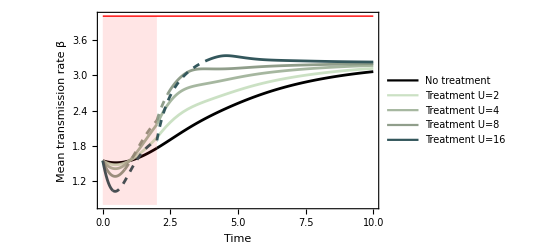

/Users/martin/Documents/lethal/figures/treatment/K4_treatment_chronic_beta_bstart0.7.pdf

InterpolatingFunction::dmval: Input value {297} lies outside the range of data in the interpolating function. Extrapolation will be used.

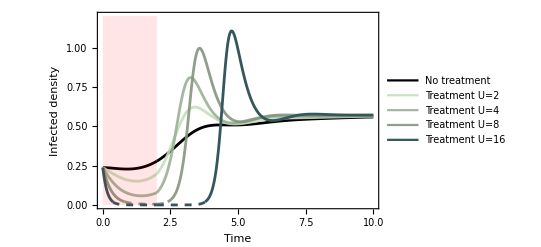

/Users/martin/Documents/lethal/figures/treatment/K4_treatment_chronic_I_bstart0.7.pdf

InterpolatingFunction::dmval: Input value {3} lies outside the range of data in the interpolating function. Extrapolation will be used.

{0.00800267}

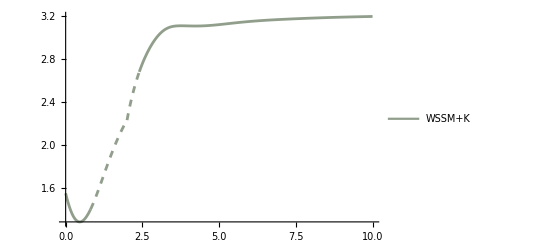

```mathematica
paramsall = {β0-> 4, α -> 2, θ -> 5, b -> 3, d -> 1,  Vs -> 1,f->0.4, λ->0.05, n->2*θ}
varsol = {g[t], v[t], 𝒮[t], ℐ[t], K3[t], K4[t]}; 

ϵ=0.02
t1=0  (*Start treatment*)
t2=2 (*stop treatment*)
t3=10

g0=0.7

betastart=4-5*g0^2
i0=b/(d+α+U*f)-d/betastart/.paramsall/.U->1
s0=(d+α+U f)/betastart/.paramsall /.U->1
U=.
temps=3
f=.
λ=.

init0={g[0]==g0,v[0]==v0,𝒮[0]==b/d,ℐ[0]==1, K3[0]==0, K4[0]==0}/.{v0->0}/.paramsall;
sol0:=NDSolve[ft[{eqs/. U-> 1,init0}]//.paramsall,varsol,{t,0,1*100}];
init={g[0]==g0,v[0]==v0,𝒮[0]==s0,ℐ[0]==i0, K3[0]==0, K4[0]==0}/.{v0->0}/.paramsall;
sol1:=NDSolve[ft[{eqs/. U-> 1,init}]//.paramsall,varsol,{t,0,t2-t1}];
sol2:=NDSolve[ft[{eqs/. U-> 2,init}]//.paramsall,varsol,{t,0,t2-t1}];
sol3:=NDSolve[ft[{eqs/. U-> 4,init}]//.paramsall,varsol,{t,0,t2-t1}];
sol4:=NDSolve[ft[{eqs/. U-> 8,init}]//.paramsall,varsol,{t,0,t2-t1}];
sol5:=NDSolve[ft[{eqs/. U->16,init}]//.paramsall,varsol,{t,0,t2-t1}];



pt1=ListPlot[{{t1,0},{t1,4}}, Joined->True, PlotStyle->Black];
pt2=ListPlot[{{t2,0},{t2,4}}, Joined->True, PlotStyle->Red];
ll = Graphics[{Red,Line[{{0,4},{t3,4}}]}];
rectraitement=Graphics[{Opacity[0.1,Red],Rectangle[{t1,0.8},{t2,4.0}]}];
text0 = Graphics[Text[Style["β_0",13,Red],{-0.9,3.96}]];


sol11 = NDSolve[ft[{eqs/. U-> 1,{g[0]==g[t]/.sol1/.t->t2-t1,v[0]==v[t]/.sol1/.t->t2-t1,K3[0]==K3[t]/.sol1/.t->t2-t1,K4[0]==K4[t]/.sol1/.t->t2-t1,𝒮[0]==𝒮[t]/.sol1/.t->t2-t1,ℐ[0]==ℐ[t]/.sol1/.t->t2-t1}/.paramsall}]//.paramsall,varsol,{t,0,t3-t2}];
sol22 = NDSolve[ft[{eqs/. U-> 1,{g[0]==g[t]/.sol2/.t->t2-t1,v[0]==v[t]/.sol2/.t->t2-t1,K3[0]==K3[t]/.sol2/.t->t2-t1,K4[0]==K4[t]/.sol2/.t->t2-t1,𝒮[0]==𝒮[t]/.sol2/.t->t2-t1,ℐ[0]==ℐ[t]/.sol2/.t->t2-t1}/.paramsall}]//.paramsall,varsol,{t,0,t3-t2}];
sol33 = NDSolve[ft[{eqs/. U-> 1,{g[0]==g[t]/.sol3/.t->t2-t1,v[0]==v[t]/.sol3/.t->t2-t1,K3[0]==K3[t]/.sol3/.t->t2-t1,K4[0]==K4[t]/.sol3/.t->t2-t1,𝒮[0]==𝒮[t]/.sol3/.t->t2-t1,ℐ[0]==ℐ[t]/.sol3/.t->t2-t1}/.paramsall}]//.paramsall,varsol,{t,0,t3-t2}];
sol44 = NDSolve[ft[{eqs/. U-> 1,{g[0]==g[t]/.sol4/.t->t2-t1,v[0]==v[t]/.sol4/.t->t2-t1,K3[0]==K3[t]/.sol4/.t->t2-t1,K4[0]==K4[t]/.sol4/.t->t2-t1,𝒮[0]==𝒮[t]/.sol4/.t->t2-t1,ℐ[0]==ℐ[t]/.sol4/.t->t2-t1}/.paramsall}]//.paramsall,varsol,{t,0,t3-t2}];
sol55 = NDSolve[ft[{eqs/. U-> 1,{g[0]==g[t]/.sol5/.t->t2-t1,v[0]==v[t]/.sol5/.t->t2-t1,K3[0]==K3[t]/.sol5/.t->t2-t1,K4[0]==K4[t]/.sol5/.t->t2-t1,𝒮[0]==𝒮[t]/.sol5/.t->t2-t1,ℐ[0]==ℐ[t]/.sol5/.t->t2-t1}/.paramsall}]//.paramsall,varsol,{t,0,t3-t2}];



pbbaru0=Plot[Evaluate[2/.sol0/.t->x/.paramsall],{x,0,1},PlotRange->{{0,t1},{1.5,3}},PlotStyle->{Dashed,Gray}];
pbbaru1=Plot[If[First[Evaluate[ℐ[t]/.sol1/.t->x-t1/.paramsall]]>ϵ,First[Evaluate[(β0-(θ (v[t]+g[t]^2))/Vs)/.sol1/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotLegends->LineLegend[{Black},{"No treatment"}], PlotStyle->Black];
pbbaru1bis=Plot[If[First[Evaluate[ℐ[t]/.sol1/.t->x-t1/.paramsall]]<ϵ,First[Evaluate[(β0-(θ (v[t]+g[t]^2))/Vs)/.sol1/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotStyle->{Dashed,Black}];
pbbaru2=Plot[If[First[Evaluate[ℐ[t]/.sol2/.t->x-t1/.paramsall]]>ϵ,First[Evaluate[(β0-(θ (v[t]+g[t]^2))/Vs)/.sol2/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotLegends->LineLegend[{c1},{"Treatment U=2"}],PlotStyle->c1];
pbbaru2bis=Plot[If[First[Evaluate[ℐ[t]/.sol2/.t->x-t1/.paramsall]]<ϵ,First[Evaluate[(β0-(θ (v[t]+g[t]^2))/Vs)/.sol2/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotStyle->{Dashed,c1}];
pbbaru3=Plot[If[First[Evaluate[ℐ[t]/.sol3/.t->x-t1/.paramsall]]>ϵ,First[Evaluate[(β0-(θ (v[t]+g[t]^2))/Vs)/.sol3/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotLegends->LineLegend[{c2},{"Treatment U=4"}],PlotStyle->c2];
pbbaru3bis=Plot[If[First[Evaluate[ℐ[t]/.sol3/.t->x-t1/.paramsall]]<ϵ,First[Evaluate[(β0-(θ (v[t]+g[t]^2))/Vs)/.sol3/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotStyle->{Dashed,c2}];
pbbaru4=Plot[If[First[Evaluate[ℐ[t]/.sol4/.t->x-t1/.paramsall]]>ϵ,First[Evaluate[(β0-(θ (v[t]+g[t]^2))/Vs)/.sol4/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotLegends->LineLegend[{c3},{"Treatment U=8"}],PlotStyle->c3];
pbbaru4bis=Plot[If[First[Evaluate[ℐ[t]/.sol4/.t->x-t1/.paramsall]]<ϵ,First[Evaluate[(β0-(θ (v[t]+g[t]^2))/Vs)/.sol4/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotStyle->{Dashed,c3}];

pbbaru5=Plot[If[First[Evaluate[ℐ[t]/.sol5/.t->x-t1/.paramsall]]>ϵ,First[Evaluate[(β0-(θ (v[t]+g[t]^2))/Vs)/.sol5/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotLegends->LineLegend[{c4},{"Treatment U=16"}],PlotStyle->c4];
pbbaru5bis=Plot[If[First[Evaluate[ℐ[t]/.sol5/.t->x-t1/.paramsall]]<ϵ,First[Evaluate[(β0-(θ (v[t]+g[t]^2))/Vs)/.sol5/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotStyle->{Dashed,c4}];



pbbaru11=Plot[If[First[Evaluate[ℐ[t]/.sol11/.t->x-t2/.paramsall]]>ϵ,Evaluate[(β0-(θ (v[t]+g[t]^2))/Vs)/.sol11/.t->x-t2/.paramsall],None],{x,t2,t3},PlotRange->All, PlotStyle->{Black}];
pbbaru11bis=Plot[If[First[Evaluate[ℐ[t]/.sol11/.t->x-t2/.paramsall]]<ϵ,Evaluate[(β0-(θ (v[t]+g[t]^2))/Vs)/.sol11/.t->x-t2/.paramsall],None],{x,t2,t3},PlotRange->All, PlotStyle->{Dashed,Black}];
pbbaru22=Plot[If[First[Evaluate[ℐ[t]/.sol22/.t->x-t2/.paramsall]]>ϵ,Evaluate[(β0-(θ (v[t]+g[t]^2))/Vs)/.sol22/.t->x-t2/.paramsall],None],{x,t2,t3},PlotRange->All, PlotStyle->{c1}];
pbbaru22bis=Plot[If[First[Evaluate[ℐ[t]/.sol22/.t->x-t2/.paramsall]]<ϵ,Evaluate[(β0-(θ (v[t]+g[t]^2))/Vs)/.sol22/.t->x-t2/.paramsall],None],{x,t2,t3},PlotRange->All, PlotStyle->{Dashed,c1}];
pbbaru33=Plot[If[First[Evaluate[ℐ[t]/.sol33/.t->x-t2/.paramsall]]>ϵ,Evaluate[(β0-(θ (v[t]+g[t]^2))/Vs)/.sol33/.t->x-t2/.paramsall],None],{x,t2,t3},PlotRange->All, PlotStyle->{c2}];
pbbaru33bis=Plot[If[First[Evaluate[ℐ[t]/.sol33/.t->x-t2/.paramsall]]<ϵ,Evaluate[(β0-(θ (v[t]+g[t]^2))/Vs)/.sol33/.t->x-t2/.paramsall],None],{x,t2,t3},PlotRange->All, PlotStyle->{Dashed,c2}];
pbbaru44=Plot[If[First[Evaluate[ℐ[t]/.sol44/.t->x-t2/.paramsall]]>ϵ,Evaluate[(β0-(θ (v[t]+g[t]^2))/Vs)/.sol44/.t->x-t2/.paramsall],None],{x,t2,t3},PlotRange->All, PlotStyle->{c3}];
pbbaru44bis=Plot[If[First[Evaluate[ℐ[t]/.sol44/.t->x-t2/.paramsall]]<ϵ,Evaluate[(β0-(θ (v[t]+g[t]^2))/Vs)/.sol44/.t->x-t2/.paramsall],None],{x,t2,t3},PlotRange->All, PlotStyle->{Dashed,c3}];
pbbaru55=Plot[If[First[Evaluate[ℐ[t]/.sol55/.t->x-t2/.paramsall]]>ϵ,Evaluate[(β0-(θ (v[t]+g[t]^2))/Vs)/.sol55/.t->x-t2/.paramsall],None],{x,t2,t3},PlotRange->All, PlotStyle->{c4}];
pbbaru55bis=Plot[If[First[Evaluate[ℐ[t]/.sol55/.t->x-t2/.paramsall]]<ϵ,Evaluate[(β0-(θ (v[t]+g[t]^2))/Vs)/.sol55/.t->x-t2/.paramsall],None],{x,t2,t3},PlotRange->All, PlotStyle->{Dashed,c4}];

Show[pbbaru1,pbbaru2,pbbaru3,pbbaru1bis,pbbaru2bis,pbbaru3bis,pbbaru4,pbbaru4bis,pbbaru5,pbbaru5bis,pbbaru11,pbbaru22,pbbaru33,pbbaru11bis,pbbaru22bis,pbbaru33bis,pbbaru44,pbbaru44bis,pbbaru55,pbbaru55bis, ll,rectraitement,Frame->{True,True,False,True},FrameStyle->{Black,Black,Automatic,Black}, FrameLabel->{Style["Time",16],Style["Mean transmission rate β̄      ",16]}, PlotRange->{{0,t3},{0.8,4}},PlotRangePadding->0, AxesOrigin->{0,1.1}, PlotRangeClipping->False, ImagePadding->50]

Export["/Users/martin/Documents/lethal/figures/treatment/K4_treatment_chronic_beta_bstart"<>ToString[g0]<>".pdf",%]



piu0=Plot[Evaluate[ℐ[t]/.sol0/.t->temps*99],{x,0,1},PlotRange->All,PlotStyle->{Dashed,Gray}];
piu1=Plot[If[First[Evaluate[ℐ[t]/.sol1/.t->x-t1/.paramsall]]>ϵ,First[Evaluate[ℐ[t]/.sol1/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->{{0,t3},{0,10}},PlotLegends->LineLegend[{Black},{"No treatment"}], PlotStyle->Black];
piu1bis=Plot[If[First[Evaluate[ℐ[t]/.sol1/.t->x-t1/.paramsall]]<ϵ,First[Evaluate[ℐ[t]/.sol1/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All, PlotStyle->{Dashed,c0}];
piu2=Plot[If[First[Evaluate[ℐ[t]/.sol2/.t->x-t1/.paramsall]]>ϵ,First[Evaluate[ℐ[t]/.sol2/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotLegends->LineLegend[{c1},{"Treatment U=2"}],PlotStyle->c1];
piu2bis=Plot[If[First[Evaluate[ℐ[t]/.sol2/.t->x-t1/.paramsall]]<ϵ,First[Evaluate[ℐ[t]/.sol2/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All, PlotStyle->{Dashed,c1}];
piu3=Plot[If[First[Evaluate[ℐ[t]/.sol3/.t->x-t1/.paramsall]]>ϵ,First[Evaluate[ℐ[t]/.sol3/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotLegends->LineLegend[{c2},{"Treatment U=4"}],PlotStyle->c2];
piu3bis=Plot[If[First[Evaluate[ℐ[t]/.sol3/.t->x-t1/.paramsall]]<ϵ,First[Evaluate[ℐ[t]/.sol3/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All, PlotStyle->{Dashed,c2}];
piu4=Plot[If[First[Evaluate[ℐ[t]/.sol4/.t->x-t1/.paramsall]]>ϵ,First[Evaluate[ℐ[t]/.sol4/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotLegends->LineLegend[{c3},{"Treatment U=8"}],PlotStyle->c3];
piu4bis=Plot[If[First[Evaluate[ℐ[t]/.sol4/.t->x-t1/.paramsall]]<ϵ,First[Evaluate[ℐ[t]/.sol4/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All, PlotStyle->{Dashed,c3}];
piu5=Plot[If[First[Evaluate[ℐ[t]/.sol5/.t->x-t1/.paramsall]]>ϵ,First[Evaluate[ℐ[t]/.sol5/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotLegends->LineLegend[{c4},{"Treatment U=16"}],PlotStyle->c4];
piu5bis=Plot[If[First[Evaluate[ℐ[t]/.sol5/.t->x-t1/.paramsall]]<ϵ,First[Evaluate[ℐ[t]/.sol5/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All, PlotStyle->{Dashed,c4}];

piu11=Plot[If[First[Evaluate[ℐ[t]/.sol11/.t->x-t2/.paramsall]]>ϵ,First[Evaluate[ℐ[t]/.sol11/.t->x-t2/.paramsall]],None],{x,t2,t3},PlotRange->{{0,t3},{0,10}}, PlotStyle->{Black}];
piu11bis=Plot[If[First[Evaluate[ℐ[t]/.sol11/.t->x-t2/.paramsall]]<ϵ,First[Evaluate[ℐ[t]/.sol11/.t->x-t2/.paramsall]],None],{x,t2,t3},PlotRange->All, PlotStyle->{Black,c0}];
piu22=Plot[If[First[Evaluate[ℐ[t]/.sol22/.t->x-t2/.paramsall]]>ϵ,First[Evaluate[ℐ[t]/.sol22/.t->x-t2/.paramsall]],None],{x,t2,t3},PlotRange->All, PlotStyle->{c1}];
piu22bis=Plot[If[First[Evaluate[ℐ[t]/.sol22/.t->x-t2/.paramsall]]<ϵ,First[Evaluate[ℐ[t]/.sol22/.t->x-t2/.paramsall]],None],{x,t2,t3},PlotRange->All, PlotStyle->{Dashed,c1}];
piu33=Plot[If[First[Evaluate[ℐ[t]/.sol33/.t->x-t2/.paramsall]]>ϵ,First[Evaluate[ℐ[t]/.sol33/.t->x-t2/.paramsall]],None],{x,t2,t3},PlotRange->All, PlotStyle->{c2}];
piu33bis=Plot[If[First[Evaluate[ℐ[t]/.sol33/.t->x-t2/.paramsall]]<ϵ,First[Evaluate[ℐ[t]/.sol33/.t->x-t2/.paramsall]],None],{x,t2,t3},PlotRange->All, PlotStyle->{Dashed,c2}];
piu44=Plot[If[First[Evaluate[ℐ[t]/.sol44/.t->x-t2/.paramsall]]>ϵ,First[Evaluate[ℐ[t]/.sol44/.t->x-t2/.paramsall]],None],{x,t2,t3},PlotRange->All, PlotStyle->{c3}];
piu44bis=Plot[If[First[Evaluate[ℐ[t]/.sol44/.t->x-t2/.paramsall]]<ϵ,First[Evaluate[ℐ[t]/.sol44/.t->x-t2/.paramsall]],None],{x,t2,t3},PlotRange->All, PlotStyle->{Dashed,c3}];
piu55=Plot[If[First[Evaluate[ℐ[t]/.sol55/.t->x-t2/.paramsall]]>ϵ,First[Evaluate[ℐ[t]/.sol55/.t->x-t2/.paramsall]],None],{x,t2,t3},PlotRange->All, PlotStyle->{c4}];
piu55bis=Plot[If[First[Evaluate[ℐ[t]/.sol55/.t->x-t2/.paramsall]]<ϵ,First[Evaluate[ℐ[t]/.sol55/.t->x-t2/.paramsall]],None],{x,t2,t3},PlotRange->All, PlotStyle->{Dashed,c4}];
rectraitement=Graphics[{Opacity[0.1,Red],Rectangle[{t1,0},{t2,1.2}]}];


Show[piu1,piu2,piu3,piu4,piu5,piu4bis,piu5bis,piu11,piu22,piu33,piu44,piu44bis,piu55,piu55bis,rectraitement, Frame->{True,True,True,True},FrameStyle->{Black,Black,Black,Black}, FrameLabel->{Style["Time",16],Style["Infected density",15]}, PlotRange->{{0,t3},{0,1.2}},PlotRangePadding->0, ImagePadding->50]
Export["/Users/martin/Documents/lethal/figures/treatment/K4_treatment_chronic_I_bstart"<>ToString[g0]<>".pdf",%]
Evaluate[ℐ[t]/.sol4/.t->temps/.paramsall]



pbbaru4=Plot[If[First[Evaluate[ℐ[t]/.sol4/.t->x-t1/.paramsall]]>ϵ,First[Evaluate[(β0-(θ (v[t]+g[t]^2))/Vs)/.sol4/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotLegends->LineLegend[{c3},{"WSSM+K"}],PlotStyle->c3];
y=Show[pbbaru4,pbbaru4bis,pbbaru44,pbbaru44bis, PlotRange->All]
```

```mathematica
eqs//.paramsall
```

{𝒮'[t]==3-(1+(4-5 (g[t]^2+v[t])) ℐ[t]) 𝒮[t],ℐ'[t]==-((3+0.4 U) ℐ[t])+(4-5 (g[t]^2+v[t])) ℐ[t] 𝒮[t],g'[t]==-1/2 (K3[t]+2 g[t] v[t]) 𝒮[t],v'[t]==0.03 U-1/2 (2 g[t] K3[t]+K4[t]+2 v[t]^2) 𝒮[t],K3'[t]==-1/2 (2 g[t] K4[t]+6 K3[t] v[t]) 𝒮[t],K4'[t]==0.0045 U-1/2 (6 K3[t]^2+8 K4[t] v[t]) 𝒮[t]}

```mathematica
eqs//.paramsall
```

{𝒮'[t]==3-(1+(4-5 (g[t]^2+v[t])) ℐ[t]) 𝒮[t],ℐ'[t]==-((3+0.4 U) ℐ[t])+(4-5 (g[t]^2+v[t])) ℐ[t] 𝒮[t],g'[t]==-1/2 (K3[t]+2 g[t] v[t]) 𝒮[t],v'[t]==0.03 U-1/2 (2 g[t] K3[t]+K4[t]+2 v[t]^2) 𝒮[t],K3'[t]==-1/2 (2 g[t] K4[t]+6 K3[t] v[t]) 𝒮[t],K4'[t]==0.0045 U-1/2 (6 K3[t]^2+8 K4[t] v[t]) 𝒮[t]}

```mathematica
sol1=NDSolve[ft[{eqs/. U-> 1,init}]//.paramsall,varsol,{t,0,t2-t1}]
```

{{g[t]→InterpolatingFunction[…][t],v[t]→InterpolatingFunction[…][t],𝒮[t]→InterpolatingFunction[…][t],ℐ[t]→InterpolatingFunction[…][t],K3[t]→InterpolatingFunction[…][t],K4[t]→InterpolatingFunction[…][t]}}

{β0→4,α→2,θ→5,b→3,d→1,Vs→1,f→0.4,λ→0.05,n→2 θ}

0.02

0

2

3

1.55

0.237192

2.19355

3

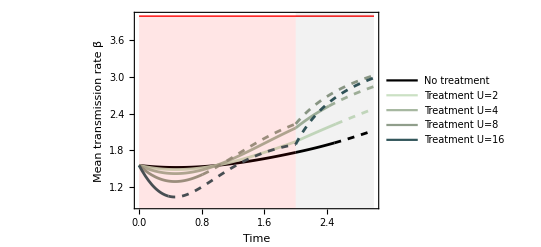

/Users/martin/Documents/lethal/figures/treatment/K4_treatment_acute_beta_bstart0.7.pdf

InterpolatingFunction::dmval: Input value {297} lies outside the range of data in the interpolating function. Extrapolation will be used.

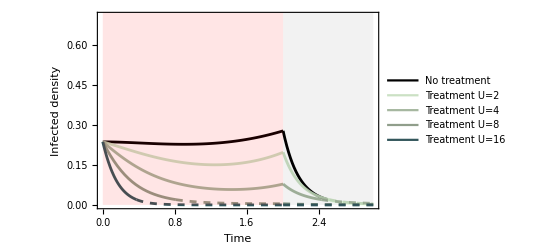

/Users/martin/Documents/lethal/figures/treatment/K4_treatment_acute_I_bstart0.7.pdf

InterpolatingFunction::dmval: Input value {3} lies outside the range of data in the interpolating function. Extrapolation will be used.

{0.00800267}

```mathematica
paramsall = {β0-> 4, α -> 2, θ -> 5, b -> 3, d -> 1,  Vs -> 1,f->0.4, λ->0.05, n->2*θ}
varsol = {g[t], v[t], 𝒮[t], ℐ[t], K3[t], K4[t]}; 

ϵ=0.02
t1=0  (*Start treatment*)
t2=2 (*stop treatment*)
t3=3



betastart=4-5*g0^2
i0=b/(d+α+U*f)-d/betastart/.paramsall/.U->1
s0=(d+α+U f)/betastart/.paramsall /.U->1
U=.
temps=3
f=.
λ=.

init0={g[0]==g0,v[0]==v0,𝒮[0]==b/d,ℐ[0]==1, K3[0]==0, K4[0]==0}/.{v0->0}/.paramsall;
sol0:=NDSolve[ft[{eqs/. U-> 1,init0}]//.paramsall,varsol,{t,0,1*100}];
init={g[0]==g0,v[0]==v0,𝒮[0]==s0,ℐ[0]==i0, K3[0]==0, K4[0]==0}/.{v0->0}/.paramsall;
sol1:=NDSolve[ft[{eqs/. U-> 1,init}]//.paramsall,varsol,{t,0,t2-t1}];
sol2:=NDSolve[ft[{eqs/. U-> 2,init}]//.paramsall,varsol,{t,0,t2-t1}];
sol3:=NDSolve[ft[{eqs/. U-> 4,init}]//.paramsall,varsol,{t,0,t2-t1}];
sol4:=NDSolve[ft[{eqs/. U-> 8,init}]//.paramsall,varsol,{t,0,t2-t1}];
sol5:=NDSolve[ft[{eqs/. U->16,init}]//.paramsall,varsol,{t,0,t2-t1}];



pt1=ListPlot[{{t1,0},{t1,4}}, Joined->True, PlotStyle->Black];
pt2=ListPlot[{{t2,0},{t2,4}}, Joined->True, PlotStyle->Red];
ll = Graphics[{Red,Line[{{0,4},{t3,4}}]}];
rectraitement=Graphics[{Opacity[0.1,Red],Rectangle[{t1,0.8},{t2,4.0}]}];
text0 = Graphics[Text[Style["β_0",13,Red],{-0.9,3.96}]];


sol11 = NDSolve[ft[{eqs/.α->αacute/. U-> 1,{g[0]==g[t]/.sol1/.t->t2-t1,v[0]==v[t]/.sol1/.t->t2-t1,K3[0]==K3[t]/.sol1/.t->t2-t1,K4[0]==K4[t]/.sol1/.t->t2-t1,𝒮[0]==𝒮[t]/.sol1/.t->t2-t1,ℐ[0]==ℐ[t]/.sol1/.t->t2-t1}/.paramsall}]//.paramsall,varsol,{t,0,t3-t2}];
sol22 = NDSolve[ft[{eqs/.α->αacute/. U-> 1,{g[0]==g[t]/.sol2/.t->t2-t1,v[0]==v[t]/.sol2/.t->t2-t1,K3[0]==K3[t]/.sol2/.t->t2-t1,K4[0]==K4[t]/.sol2/.t->t2-t1,𝒮[0]==𝒮[t]/.sol2/.t->t2-t1,ℐ[0]==ℐ[t]/.sol2/.t->t2-t1}/.paramsall}]//.paramsall,varsol,{t,0,t3-t2}];
sol33 = NDSolve[ft[{eqs/.α->αacute/. U-> 1,{g[0]==g[t]/.sol3/.t->t2-t1,v[0]==v[t]/.sol3/.t->t2-t1,K3[0]==K3[t]/.sol3/.t->t2-t1,K4[0]==K4[t]/.sol3/.t->t2-t1,𝒮[0]==𝒮[t]/.sol3/.t->t2-t1,ℐ[0]==ℐ[t]/.sol3/.t->t2-t1}/.paramsall}]//.paramsall,varsol,{t,0,t3-t2}];
sol44 = NDSolve[ft[{eqs/.α->αacute/. U-> 1,{g[0]==g[t]/.sol4/.t->t2-t1,v[0]==v[t]/.sol4/.t->t2-t1,K3[0]==K3[t]/.sol4/.t->t2-t1,K4[0]==K4[t]/.sol4/.t->t2-t1,𝒮[0]==𝒮[t]/.sol4/.t->t2-t1,ℐ[0]==ℐ[t]/.sol4/.t->t2-t1}/.paramsall}]//.paramsall,varsol,{t,0,t3-t2}];
sol55 = NDSolve[ft[{eqs/.α->αacute/. U-> 1,{g[0]==g[t]/.sol5/.t->t2-t1,v[0]==v[t]/.sol5/.t->t2-t1,K3[0]==K3[t]/.sol5/.t->t2-t1,K4[0]==K4[t]/.sol5/.t->t2-t1,𝒮[0]==𝒮[t]/.sol5/.t->t2-t1,ℐ[0]==ℐ[t]/.sol5/.t->t2-t1}/.paramsall}]//.paramsall,varsol,{t,0,t3-t2}];



pbbaru0=Plot[Evaluate[2/.sol0/.t->x/.paramsall],{x,0,1},PlotRange->{{0,t1},{1.5,3}},PlotStyle->{Dashed,Gray}];
pbbaru1=Plot[If[First[Evaluate[ℐ[t]/.sol1/.t->x-t1/.paramsall]]>ϵ,First[Evaluate[(β0-(θ (v[t]+g[t]^2))/Vs)/.sol1/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotLegends->LineLegend[{Black},{"No treatment"}], PlotStyle->Black];
pbbaru1bis=Plot[If[First[Evaluate[ℐ[t]/.sol1/.t->x-t1/.paramsall]]<ϵ,First[Evaluate[(β0-(θ (v[t]+g[t]^2))/Vs)/.sol1/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotStyle->{Dashed,Black}];
pbbaru2=Plot[If[First[Evaluate[ℐ[t]/.sol2/.t->x-t1/.paramsall]]>ϵ,First[Evaluate[(β0-(θ (v[t]+g[t]^2))/Vs)/.sol2/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotLegends->LineLegend[{c1},{"Treatment U=2"}],PlotStyle->c1];
pbbaru2bis=Plot[If[First[Evaluate[ℐ[t]/.sol2/.t->x-t1/.paramsall]]<ϵ,First[Evaluate[(β0-(θ (v[t]+g[t]^2))/Vs)/.sol2/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotStyle->{Dashed,c1}];
pbbaru3=Plot[If[First[Evaluate[ℐ[t]/.sol3/.t->x-t1/.paramsall]]>ϵ,First[Evaluate[(β0-(θ (v[t]+g[t]^2))/Vs)/.sol3/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotLegends->LineLegend[{c2},{"Treatment U=4"}],PlotStyle->c2];
pbbaru3bis=Plot[If[First[Evaluate[ℐ[t]/.sol3/.t->x-t1/.paramsall]]<ϵ,First[Evaluate[(β0-(θ (v[t]+g[t]^2))/Vs)/.sol3/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotStyle->{Dashed,c2}];
pbbaru4=Plot[If[First[Evaluate[ℐ[t]/.sol4/.t->x-t1/.paramsall]]>ϵ,First[Evaluate[(β0-(θ (v[t]+g[t]^2))/Vs)/.sol4/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotLegends->LineLegend[{c3},{"Treatment U=8"}],PlotStyle->c3];
pbbaru4bis=Plot[If[First[Evaluate[ℐ[t]/.sol4/.t->x-t1/.paramsall]]<ϵ,First[Evaluate[(β0-(θ (v[t]+g[t]^2))/Vs)/.sol4/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotStyle->{Dashed,c3}];

pbbaru5=Plot[If[First[Evaluate[ℐ[t]/.sol5/.t->x-t1/.paramsall]]>ϵ,First[Evaluate[(β0-(θ (v[t]+g[t]^2))/Vs)/.sol5/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotLegends->LineLegend[{c4},{"Treatment U=16"}],PlotStyle->c4];
pbbaru5bis=Plot[If[First[Evaluate[ℐ[t]/.sol5/.t->x-t1/.paramsall]]<ϵ,First[Evaluate[(β0-(θ (v[t]+g[t]^2))/Vs)/.sol5/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotStyle->{Dashed,c4}];



pbbaru11=Plot[If[First[Evaluate[ℐ[t]/.sol11/.t->x-t2/.paramsall]]>ϵ,Evaluate[(β0-(θ (v[t]+g[t]^2))/Vs)/.sol11/.t->x-t2/.paramsall],None],{x,t2,t3},PlotRange->All, PlotStyle->{Black}];
pbbaru11bis=Plot[If[First[Evaluate[ℐ[t]/.sol11/.t->x-t2/.paramsall]]<ϵ,Evaluate[(β0-(θ (v[t]+g[t]^2))/Vs)/.sol11/.t->x-t2/.paramsall],None],{x,t2,t3},PlotRange->All, PlotStyle->{Dashed,Black}];
pbbaru22=Plot[If[First[Evaluate[ℐ[t]/.sol22/.t->x-t2/.paramsall]]>ϵ,Evaluate[(β0-(θ (v[t]+g[t]^2))/Vs)/.sol22/.t->x-t2/.paramsall],None],{x,t2,t3},PlotRange->All, PlotStyle->{c1}];
pbbaru22bis=Plot[If[First[Evaluate[ℐ[t]/.sol22/.t->x-t2/.paramsall]]<ϵ,Evaluate[(β0-(θ (v[t]+g[t]^2))/Vs)/.sol22/.t->x-t2/.paramsall],None],{x,t2,t3},PlotRange->All, PlotStyle->{Dashed,c1}];
pbbaru33=Plot[If[First[Evaluate[ℐ[t]/.sol33/.t->x-t2/.paramsall]]>ϵ,Evaluate[(β0-(θ (v[t]+g[t]^2))/Vs)/.sol33/.t->x-t2/.paramsall],None],{x,t2,t3},PlotRange->All, PlotStyle->{c2}];
pbbaru33bis=Plot[If[First[Evaluate[ℐ[t]/.sol33/.t->x-t2/.paramsall]]<ϵ,Evaluate[(β0-(θ (v[t]+g[t]^2))/Vs)/.sol33/.t->x-t2/.paramsall],None],{x,t2,t3},PlotRange->All, PlotStyle->{Dashed,c2}];
pbbaru44=Plot[If[First[Evaluate[ℐ[t]/.sol44/.t->x-t2/.paramsall]]>ϵ,Evaluate[(β0-(θ (v[t]+g[t]^2))/Vs)/.sol44/.t->x-t2/.paramsall],None],{x,t2,t3},PlotRange->All, PlotStyle->{c3}];
pbbaru44bis=Plot[If[First[Evaluate[ℐ[t]/.sol44/.t->x-t2/.paramsall]]<ϵ,Evaluate[(β0-(θ (v[t]+g[t]^2))/Vs)/.sol44/.t->x-t2/.paramsall],None],{x,t2,t3},PlotRange->All, PlotStyle->{Dashed,c3}];
pbbaru55=Plot[If[First[Evaluate[ℐ[t]/.sol55/.t->x-t2/.paramsall]]>ϵ,Evaluate[(β0-(θ (v[t]+g[t]^2))/Vs)/.sol55/.t->x-t2/.paramsall],None],{x,t2,t3},PlotRange->All, PlotStyle->{c4}];
pbbaru55bis=Plot[If[First[Evaluate[ℐ[t]/.sol55/.t->x-t2/.paramsall]]<ϵ,Evaluate[(β0-(θ (v[t]+g[t]^2))/Vs)/.sol55/.t->x-t2/.paramsall],None],{x,t2,t3},PlotRange->All, PlotStyle->{Dashed,c4}];

Show[pbbaru1,pbbaru2,pbbaru3,pbbaru1bis,pbbaru2bis,pbbaru3bis,pbbaru4,pbbaru4bis,pbbaru5,pbbaru5bis,pbbaru11,pbbaru22,pbbaru33,pbbaru11bis,pbbaru22bis,pbbaru33bis,pbbaru44,pbbaru44bis,pbbaru55,pbbaru55bis, ll,rectraitement,recacute,text0,Frame->{True,True,False,True},FrameStyle->{Black,Black,Automatic,Black}, FrameLabel->{Style["Time",16],Style["Mean transmission rate β̄      ",16]}, PlotRange->{{0,t3},{0.9,4}},PlotRangePadding->0, AxesOrigin->{0,1.1}, ImagePadding->50]

Export["/Users/martin/Documents/lethal/figures/treatment/K4_treatment_acute_beta_bstart"<>ToString[g0]<>".pdf",%]



piu0=Plot[Evaluate[ℐ[t]/.sol0/.t->temps*99],{x,0,1},PlotRange->All,PlotStyle->{Dashed,Gray}];
piu1=Plot[If[First[Evaluate[ℐ[t]/.sol1/.t->x-t1/.paramsall]]>ϵ,First[Evaluate[ℐ[t]/.sol1/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->{{0,t3},{0,10}},PlotLegends->LineLegend[{Black},{"No treatment"}], PlotStyle->Black];
piu1bis=Plot[If[First[Evaluate[ℐ[t]/.sol1/.t->x-t1/.paramsall]]<ϵ,First[Evaluate[ℐ[t]/.sol1/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All, PlotStyle->{Dashed,c0}];
piu2=Plot[If[First[Evaluate[ℐ[t]/.sol2/.t->x-t1/.paramsall]]>ϵ,First[Evaluate[ℐ[t]/.sol2/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotLegends->LineLegend[{c1},{"Treatment U=2"}],PlotStyle->c1];
piu2bis=Plot[If[First[Evaluate[ℐ[t]/.sol2/.t->x-t1/.paramsall]]<ϵ,First[Evaluate[ℐ[t]/.sol2/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All, PlotStyle->{Dashed,c1}];
piu3=Plot[If[First[Evaluate[ℐ[t]/.sol3/.t->x-t1/.paramsall]]>ϵ,First[Evaluate[ℐ[t]/.sol3/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotLegends->LineLegend[{c2},{"Treatment U=4"}],PlotStyle->c2];
piu3bis=Plot[If[First[Evaluate[ℐ[t]/.sol3/.t->x-t1/.paramsall]]<ϵ,First[Evaluate[ℐ[t]/.sol3/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All, PlotStyle->{Dashed,c2}];
piu4=Plot[If[First[Evaluate[ℐ[t]/.sol4/.t->x-t1/.paramsall]]>ϵ,First[Evaluate[ℐ[t]/.sol4/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotLegends->LineLegend[{c3},{"Treatment U=8"}],PlotStyle->c3];
piu4bis=Plot[If[First[Evaluate[ℐ[t]/.sol4/.t->x-t1/.paramsall]]<ϵ,First[Evaluate[ℐ[t]/.sol4/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All, PlotStyle->{Dashed,c3}];
piu5=Plot[If[First[Evaluate[ℐ[t]/.sol5/.t->x-t1/.paramsall]]>ϵ,First[Evaluate[ℐ[t]/.sol5/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All,PlotLegends->LineLegend[{c4},{"Treatment U=16"}],PlotStyle->c4];
piu5bis=Plot[If[First[Evaluate[ℐ[t]/.sol5/.t->x-t1/.paramsall]]<ϵ,First[Evaluate[ℐ[t]/.sol5/.t->x-t1/.paramsall]],None],{x,t1,t2},PlotRange->All, PlotStyle->{Dashed,c4}];

piu11=Plot[If[First[Evaluate[ℐ[t]/.sol11/.t->x-t2/.paramsall]]>ϵ,First[Evaluate[ℐ[t]/.sol11/.t->x-t2/.paramsall]],None],{x,t2,t3},PlotRange->{{0,t3},{0,10}}, PlotStyle->{Black}];
piu11bis=Plot[If[First[Evaluate[ℐ[t]/.sol11/.t->x-t2/.paramsall]]<ϵ,First[Evaluate[ℐ[t]/.sol11/.t->x-t2/.paramsall]],None],{x,t2,t3},PlotRange->All, PlotStyle->{Black,c0}];
piu22=Plot[If[First[Evaluate[ℐ[t]/.sol22/.t->x-t2/.paramsall]]>ϵ,First[Evaluate[ℐ[t]/.sol22/.t->x-t2/.paramsall]],None],{x,t2,t3},PlotRange->All, PlotStyle->{c1}];
piu22bis=Plot[If[First[Evaluate[ℐ[t]/.sol22/.t->x-t2/.paramsall]]<ϵ,First[Evaluate[ℐ[t]/.sol22/.t->x-t2/.paramsall]],None],{x,t2,t3},PlotRange->All, PlotStyle->{Dashed,c1}];
piu33=Plot[If[First[Evaluate[ℐ[t]/.sol33/.t->x-t2/.paramsall]]>ϵ,First[Evaluate[ℐ[t]/.sol33/.t->x-t2/.paramsall]],None],{x,t2,t3},PlotRange->All, PlotStyle->{c2}];
piu33bis=Plot[If[First[Evaluate[ℐ[t]/.sol33/.t->x-t2/.paramsall]]<ϵ,First[Evaluate[ℐ[t]/.sol33/.t->x-t2/.paramsall]],None],{x,t2,t3},PlotRange->All, PlotStyle->{Dashed,c2}];
piu44=Plot[If[First[Evaluate[ℐ[t]/.sol44/.t->x-t2/.paramsall]]>ϵ,First[Evaluate[ℐ[t]/.sol44/.t->x-t2/.paramsall]],None],{x,t2,t3},PlotRange->All, PlotStyle->{c3}];
piu44bis=Plot[If[First[Evaluate[ℐ[t]/.sol44/.t->x-t2/.paramsall]]<ϵ,First[Evaluate[ℐ[t]/.sol44/.t->x-t2/.paramsall]],None],{x,t2,t3},PlotRange->All, PlotStyle->{Dashed,c3}];
piu55=Plot[If[First[Evaluate[ℐ[t]/.sol55/.t->x-t2/.paramsall]]>ϵ,First[Evaluate[ℐ[t]/.sol55/.t->x-t2/.paramsall]],None],{x,t2,t3},PlotRange->All, PlotStyle->{c4}];
piu55bis=Plot[If[First[Evaluate[ℐ[t]/.sol55/.t->x-t2/.paramsall]]<ϵ,First[Evaluate[ℐ[t]/.sol55/.t->x-t2/.paramsall]],None],{x,t2,t3},PlotRange->All, PlotStyle->{Dashed,c4}];
rectraitement=Graphics[{Opacity[0.1,Red],Rectangle[{t1,0},{t2,1.2}]}];


Show[piu11,piu1,piu2,piu3,piu1bis,piu2bis,piu3bis,piu4,piu4bis,piu5,piu5bis,piu22,piu33,piu11bis,piu22bis,piu33bis,piu44,piu44bis,piu55,piu55bis,rectraitement,recacute, Frame->{True,True,True,True},FrameStyle->{Black,Black,Black,Black}, FrameLabel->{Style["Time",15],Style["Infected density",16]}, PlotRange->{{0,t3},{0,0.71}},PlotRangePadding->0, ImagePadding->50]
Export["/Users/martin/Documents/lethal/figures/treatment/K4_treatment_acute_I_bstart"<>ToString[g0]<>".pdf",%]
Evaluate[ℐ[t]/.sol4/.t->temps/.paramsall]
```

#### K4 β̄

0.15

0.032

80

0.4

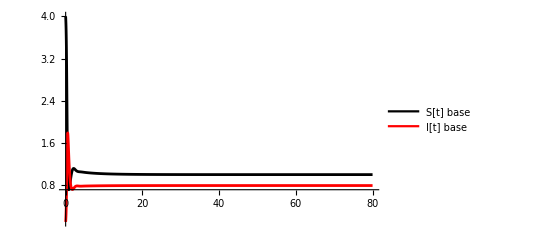

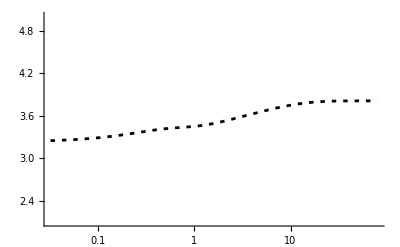

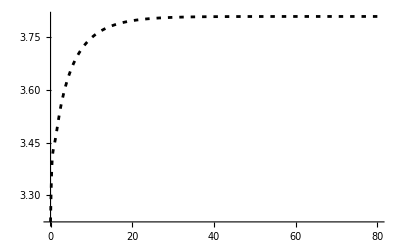

3.225

```mathematica
varsol = {g[t], v[t], 𝒮[t], ℐ[t], K3[t], K4[t]}; 
paramsall = {Vs->1,λ->0.005,n->5,β0 -> 4, α -> 2, b -> 4, d -> 1, U->2, f->0.4,θ->5/2};

sigmastart=0.15

t0l=0.032
temps=80


βbar[t_]:=Subscript[β, m][t]-(n σ[t])/(2 Vs)/.paramsall;

g0=0.4


init={g[0]==g0,v[0]==v0,𝒮[0]==b/d,ℐ[0]==0.1, K3[0]==0, K4[0]==0}/.{v0->sigmastart}/.paramsall;

sol:=NDSolve[ft[{eqs,init}]//.paramsall,varsol,{t,0,temps}];

ps12=Plot[Evaluate[𝒮[t]/. sol],{t,0,temps},PlotRange->All,PlotStyle->{Black},PlotLegends->LineLegend[{Directive[Black]},{"S[t] "<>scenario}]];
pi12=Plot[Evaluate[ℐ[t]/. sol],{t,0,temps},PlotRange->All,PlotStyle->{Red},PlotLegends->LineLegend[{Directive[Red]},{"I[t] "<>scenario}]];
pepi12=Show[ps12,pi12]


pbbar12l=LogLinearPlot[Evaluate[(β0-(θ (v[t]+g[t]^2))/Vs)/.paramsall/.sol//First],{t,t0l,temps},PlotRange->{All,{2.1,5}},PlotStyle->{Black, Dashing[{0.008,Small}]}]
pbbar12=Plot[Evaluate[(β0-(θ (v[t]+g[t]^2))/Vs)/.paramsall/.sol//First],{t,0,temps},PlotRange->All,PlotStyle->{Black, Dashing[{0.008,Small}]}]
(β0-(θ (v[t]+g[t]^2))/Vs)/.paramsall/.sol/.t->0//First/.t->0
```

```mathematica
{eqs,init}//.paramsall
```

{{𝒮'[t]==4-(1+(4-5/2 (g[t]^2+v[t])) ℐ[t]) 𝒮[t],ℐ'[t]==-3.8 ℐ[t]+(4-5/2 (g[t]^2+v[t])) ℐ[t] 𝒮[t],g'[t]==-1/2 (K3[t]+2 g[t] v[t]) 𝒮[t],v'[t]==0.006-1/2 (2 g[t] K3[t]+K4[t]+2 v[t]^2) 𝒮[t],K3'[t]==-1/2 (2 g[t] K4[t]+6 K3[t] v[t]) 𝒮[t],K4'[t]==0.00009-1/2 (6 K3[t]^2+8 K4[t] v[t]) 𝒮[t]},{g[0]==0.4,v[0]==0.15,𝒮[0]==4,ℐ[0]==0.1,K3[0]==0,K4[0]==0}}

0.7

-Graphics-

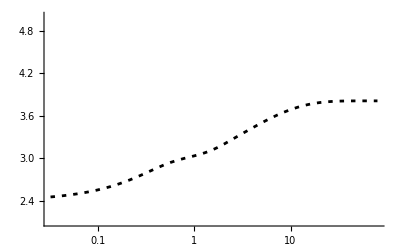

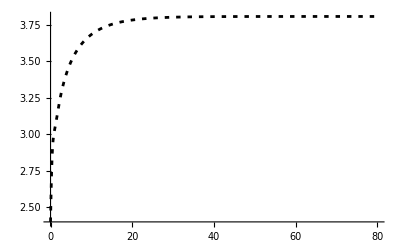

2.4

```mathematica
g0=0.7


init={g[0]==g0,v[0]==v0,𝒮[0]==b/d,ℐ[0]==0.1, K3[0]==0, K4[0]==0}/.{v0->sigmastart}/.paramsall;

sol:=NDSolve[ft[{eqs,init}]//.paramsall,varsol,{t,0,temps}];

ps10=Plot[Evaluate[𝒮[t]/. sol],{t,0,temps},PlotRange->All,PlotStyle->{Black},PlotLegends->LineLegend[{Directive[Black]},{"S[t] "<>scenario}]];
pi10=Plot[Evaluate[ℐ[t]/. sol],{t,0,temps},PlotRange->All,PlotStyle->{Red},PlotLegends->LineLegend[{Directive[Red]},{"I[t] "<>scenario}]];
pepi10=Show[ps12,pi12]


pbbar10l=LogLinearPlot[Evaluate[(β0-(θ (v[t]+g[t]^2))/Vs)/.paramsall/.sol//First],{t,t0l,temps},PlotRange->{All,{2.1,5}},PlotStyle->{Black, Dashing[{0.008,Small}]}]
pbbar10=Plot[Evaluate[(β0-(θ (v[t]+g[t]^2))/Vs)/.paramsall/.sol//First],{t,0,temps},PlotRange->All,PlotStyle->{Black, Dashing[{0.008,Small}]}]
(β0-(θ (v[t]+g[t]^2))/Vs)/.paramsall/.sol/.t->0//First/.t->0
```

0.4

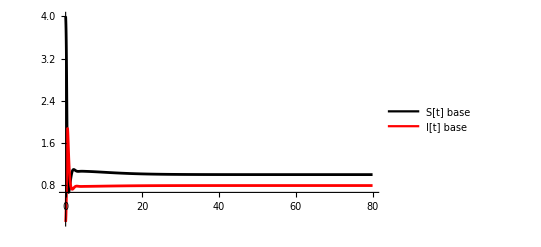

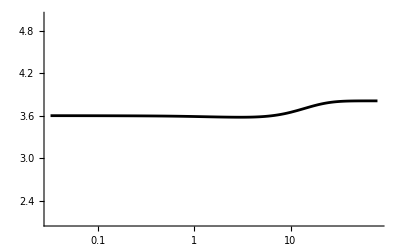

3.6

```mathematica
g0=0.4


init={g[0]==g0,v[0]==v0,𝒮[0]==b/d,ℐ[0]==0.1, K3[0]==0, K4[0]==0}/.{v0->0}/.paramsall;

sol:=NDSolve[ft[{eqs,init}]//.paramsall,varsol,{t,0,temps}];

ps12=Plot[Evaluate[𝒮[t]/. sol],{t,0,temps},PlotRange->All,PlotStyle->{Black},PlotLegends->LineLegend[{Directive[Black]},{"S[t] "<>scenario}]];
pi12=Plot[Evaluate[ℐ[t]/. sol],{t,0,temps},PlotRange->All,PlotStyle->{Red},PlotLegends->LineLegend[{Directive[Red]},{"I[t] "<>scenario}]];
pepi12=Show[ps12,pi12]


pbbar6l=LogLinearPlot[Evaluate[(β0-(θ (v[t]+g[t]^2))/Vs)/.paramsall/.sol//First],{t,t0l,temps},PlotRange->{All,{2.1,5}},PlotStyle->{Black}]
pbbar6=Plot[Evaluate[(β0-(θ (v[t]+g[t]^2))/Vs)/.paramsall/.sol//First],{t,0,temps},PlotRange->All,PlotStyle->{Black, Dashing[{0.008,Small}]}];
(β0-(θ (v[t]+g[t]^2))/Vs)/.paramsall/.sol/.t->0//First/.t->0
```

0.7

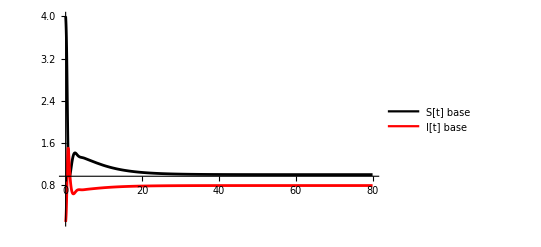

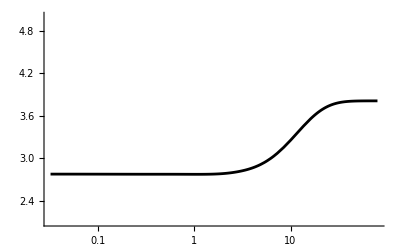

2.775

3.8085

```mathematica
g0=0.7


init={g[0]==g0,v[0]==v0,𝒮[0]==b/d,ℐ[0]==0.1, K3[0]==0, K4[0]==0}/.{v0->0}/.paramsall;

sol:=NDSolve[ft[{eqs,init}]//.paramsall,varsol,{t,0,temps}];

ps12=Plot[Evaluate[𝒮[t]/. sol],{t,0,temps},PlotRange->All,PlotStyle->{Black},PlotLegends->LineLegend[{Directive[Black]},{"S[t] "<>scenario}]];
pi12=Plot[Evaluate[ℐ[t]/. sol],{t,0,temps},PlotRange->All,PlotStyle->{Red},PlotLegends->LineLegend[{Directive[Red]},{"I[t] "<>scenario}]];
pepi12=Show[ps12,pi12]


pbbar8l=LogLinearPlot[Evaluate[(β0-(θ (v[t]+g[t]^2))/Vs)/.paramsall/.sol//First],{t,t0l,temps},PlotRange->{All,{2.1,5}},PlotStyle->{Black}]
pbbar8=Plot[Evaluate[(β0-(θ (v[t]+g[t]^2))/Vs)/.paramsall/.sol//First],{t,0,temps},PlotRange->All,PlotStyle->{Black, Dashing[{0.008,Small}]}];

(β0-(θ (v[t]+g[t]^2))/Vs)/.paramsall/.sol/.t->0//First/.t->0
(β0-(θ (v[t]+g[t]^2))/Vs)/.paramsall/.sol/.t->temps//First/.t->temps
```

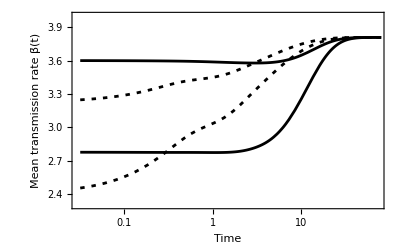

/Users/martin/Documents/lethal/figures/betabar/diffbeta_diffsigma_log-K4.pdf

{Vs→1,λ→0.005,n→5,β0→4,α→2,b→4,d→1,U→2,f→0.4,θ→5/2}

```mathematica
text0 = Graphics[Text[Style["β_0",13],{-3.4,4.03}]];
text1 = Graphics[Text[Style["L_M^*",13],{42,3.9}]];
text2 = Graphics[Text[Style["L_M(0)",13],{0.05,3.4}]];
arr = Graphics[{Gray,Thick,{Arrowheads[Medium],Arrow[{{40,4},{40,3.78}}]}}];
ll = Graphics[{Gray,Thick,Line[{{40,4},{0,4}}]}];



text0 = Graphics[Text[Style["β_0",13,Red],{-4.15,4.02}]];
text1 = Graphics[Text[Style["L_M^*",13],{4.8,3.9}]];
text2 = Graphics[Text[Style["L_M(0)",13],{-2.7,3.35}]];
arr2 = Graphics[{Opacity[0.5,Red],Thick,{Arrowheads[Medium],Arrow[{{-3.35,3.52},{-3.35,3.2}}]}}];
text3 = Graphics[Text[Style["L_L(0)",13],{-2.7,3.75}]];
arr3 = Graphics[{Opacity[0.5,Red],Thick,{Arrowheads[Medium],Arrow[{{-3.35,4},{-3.35,3.55}}]}}];
arr = Graphics[{Opacity[0.5,Red],Thick,{Arrowheads[Medium],Arrow[{{4.35,4},{4.35,3.80}}]}}];
ll = Graphics[{Red,Thick,Line[{{4.35,4},{-3.4,4}}]}];


Show[pbbar12l,pbbar10l,pbbar8l,pbbar6l(*,text0,arr,ll,text1 ,text2,text3,arr3,arr2*), Frame->{True,True,False,False},FrameStyle->{Black,Black,Black}, FrameLabel->{Style["Time",13],Style["Mean transmission rate β̄(t)",13]}, PlotRange->{{-3.5,4.3},{2.3,4.0}},ImagePadding->45
, ImageSize->400,PlotRangeClipping->False,PlotRangePadding->0]
Export["/Users/martin/Documents/lethal/figures/betabar/diffbeta_diffsigma_log-K4.pdf",%]
paramsall
```

```mathematica
K3[t]/.sol//First
```

InterpolatingFunction[…][t]

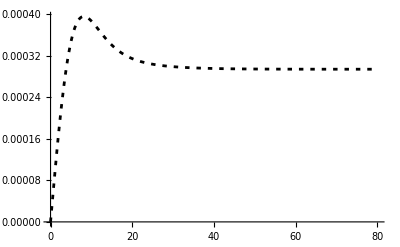

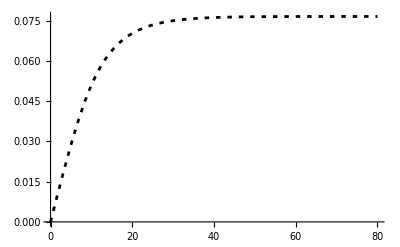

```mathematica
Plot[Evaluate[K4[t]/.paramsall/.sol//First],{t,0,temps},PlotRange->All,PlotStyle->{Black, Dashing[{0.008,Small}]}]
Plot[Evaluate[v[t]/.paramsall/.sol//First],{t,0,temps},PlotRange->All,PlotStyle->{Black, Dashing[{0.008,Small}]}]
```